# Cubic best-approximation interpolating splines for RealSolarSystem

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
<<"splines`"
```

## ISA model

## Atmosphere model.

### Constants (SI units).

```mathematica
g0=9.80665;
Rstar=8.31432;
Mair=0.0289644;
atm=101325.;
Celsius0=273.15;
meanEarthRadius=6371009.;
km=1000.;
```

```mathematica
geopotentialHeight[h_]:=(meanEarthRadius h)/(meanEarthRadius+h)
```

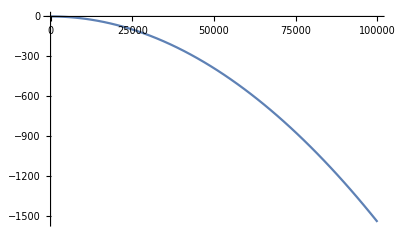

```mathematica
Plot[geopotentialHeight[h]-h,{h,0,100000}]
```

### Barometric formula.

```mathematica
barometricPressure[Pb_,Tb_,Lb_,h_,hb_]:=
Piecewise[{{Pb(Tb/(Tb+Lb(h-hb)))^((g0 Mair)/(Rstar Lb)), Lb≠0}, {Pb ⅇ^((-g0 Mair(h-hb))/(Rstar Tb)), Lb==0}}]
```

### International Standard Atmosphere (1976)—extended above the mesopause by careful eyeballing from a graph of dubious provenance.

#### Temperature as a function of geopotential altitude:

```mathematica
TTroposphere[h_]:=
15+Celsius0-6.5h/km;
TTropopause[h_]:=
TTroposphere[11000];
TLowStratosphere[h_]:=
TTropopause[20000]+(h-20000)/km;
THighStratosphere[h_]:=
TLowStratosphere[32000]+2.8(h-32000)/km;
TStratopause[h_]:=
THighStratosphere[47000];
TLowMesosphere[h_]:=
TStratopause[51000]-2.8(h-51000)/km;
THighMesosphere[h_]:=
TLowMesosphere[71000]-2.0(h-71000)/km;
TMesopause[h_]:=
THighMesosphere[84852]
TThermosphere[h_]:=
TMesopause[90000]+(h-90000)/km
```

```mathematica
TGeopot[h_]:=Piecewise[{{TTroposphere[h], -1≤h<11000.}, {TTropopause[h], 11000≤h<20000.}, {TLowStratosphere[h], 20000≤h<32000.}, {THighStratosphere[h], 32000≤h<47000.}, {TStratopause[h], 47000≤h<51000.}, {TLowMesosphere[h], 51000≤h<71000.}, {THighMesosphere[h], 71000≤h<84852.}, {TMesopause[h], 84852≤h<90000.}, {TThermosphere[h], 90000.≤h}}]
```

```mathematica
T[h_]:=TGeopot[geopotentialHeight[h]];
```

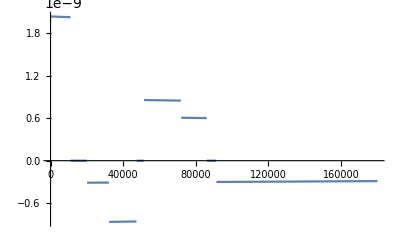

```mathematica
Plot[T''[h],{h,0,180km}]
```

### Pressure as a function of geopotential altitude.

```mathematica
pTroposphere[h_]:=barometricPressure[
101325,TTroposphere[0],-6.5/1000,h,0];
pTropopause[h_]:=barometricPressure[
pTroposphere[11000],TTropopause[11000],
0./1000,h,11000];
pLowStratosphere[h_]:=barometricPressure[
pTropopause[20000],TLowStratosphere[20000],
1/1000,h,20000];
pHighStratosphere[h_]:=barometricPressure[
pLowStratosphere[32000],THighStratosphere[32000],
2.8/1000,h,32000];
pStratopause[h_]:=barometricPressure[
pHighStratosphere[47000],TStratopause[47000],
0/1000,h,47000];
pLowMesosphere[h_]:=barometricPressure[
pStratopause[51000],TLowMesosphere[51000],
-2.8/1000,h,51000];
pHighMesosphere[h_]:=barometricPressure[
pLowMesosphere[71000],THighMesosphere[71000],
-2.0/1000,h,71000];
pMesopause[h_]:=barometricPressure[
pHighMesosphere[84852],TMesopause[84852],
-2.0/1000,h,84852];
pThermosphere[h_]:=barometricPressure[
pMesopause[90000],TThermosphere[90000],
1/1000,h,90000];
```

```mathematica
pGeopot[h_]:=Piecewise[{{pTroposphere[h], -1≤h<11000.}, {pTropopause[h], 11000≤h<20000.}, {pLowStratosphere[h], 20000≤h<32000.}, {pHighStratosphere[h], 32000≤h<47000.}, {pStratopause[h], 47000≤h<51000.}, {pLowMesosphere[h], 51000≤h<71000.}, {pHighMesosphere[h], 71000≤h<84852.}, {pMesopause[h], 84852≤h<90000.}, {pThermosphere[h], 90000.≤h}}]
```

```mathematica
boundsGeopot={
0,11000,20000,32000,47000,
51000,71000,84852,90000};
```

```mathematica
pLayers=Composition[#,geopotentialHeight]&/@{pTroposphere,pTropopause,pLowStratosphere,pHighStratosphere,pStratopause,pLowMesosphere,pHighMesosphere,pMesopause,pThermosphere};
```

### Pressure as a function of geometric altitude.

```mathematica
p[h_]:=pGeopot[geopotentialHeight[h]]
```

```mathematica
bounds=Append[
h/@boundsGeopot /.
NSolve[geopotentialHeight[h/@boundsGeopot]==
boundsGeopot]⟦1⟧,
180km
];
Clear[h]
```

### Temperature utilities

```mathematica
TLayers=Composition[#,geopotentialHeight]&/@{TTroposphere,TTropopause,TLowStratosphere,THighStratosphere,TStratopause,TLowMesosphere,THighMesosphere,TMesopause,TThermosphere};
```

### Visualisations.

#### Temperature.

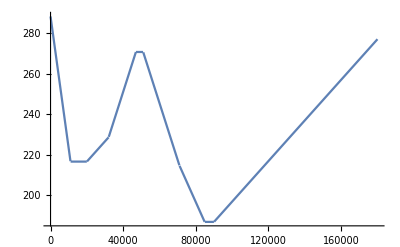

```mathematica
Plot[TGeopot[h],{h,0,180km}]
```

#### Plots of P (logarithmic and linear), ⅆP/ⅆh, (ⅆ^2 P)/(ⅆ h^2), (ⅆ^2 P)/(ⅆ h^2), (ⅆ^3 P)/(ⅆ h^3), (ⅆ^4 P)/(ⅆ h^4), (|1/((ⅆ^4 P)/(ⅆ h^4))|)^(1/4).

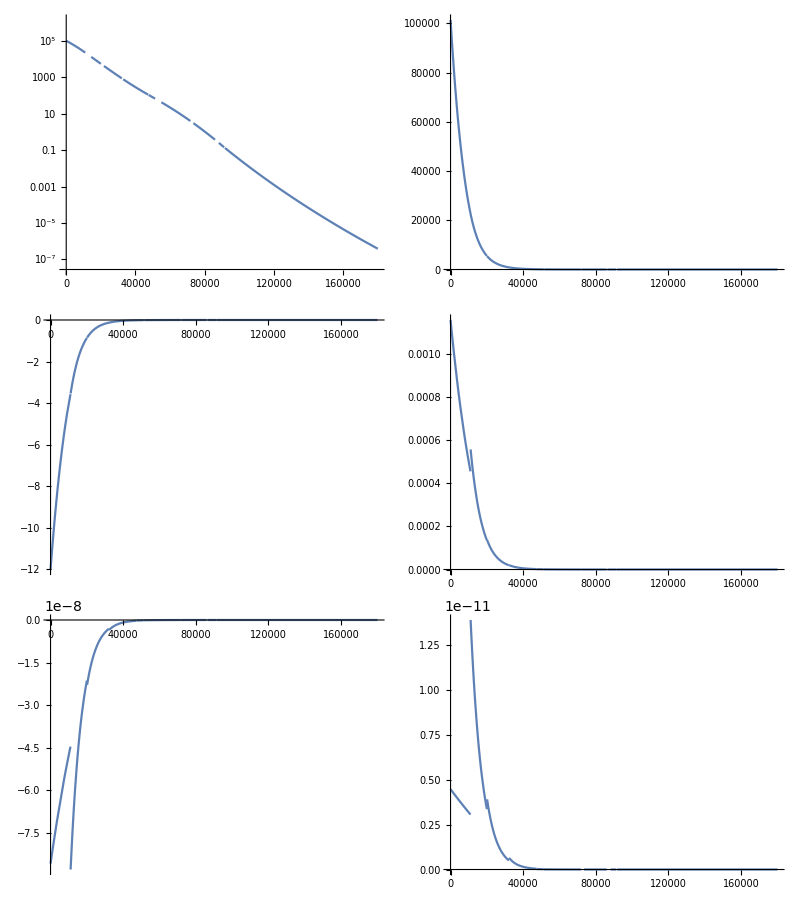

```mathematica
TableForm[Partition[
{LogPlot[p[h],{h,0,180000},PlotRange->Full],
Plot[p[h],{h,0,180000},PlotRange->Full],
Plot[p'[h],{h,0,180000},PlotRange->Full],
Plot[p''[h],{h,0,180000},PlotRange->Full],
Plot[p'''[h],{h,0,180000},PlotRange->Full],
Plot[p''''[h],{h,0,180000},PlotRange->Full],
Plot[1/p''''[h]^(1/4),{h,0,180000},PlotRange->Full]
},2]]
```

#### The step length heuristic, (|P/((ⅆ^4 P)/(ⅆ h^4))|)^(1/4).

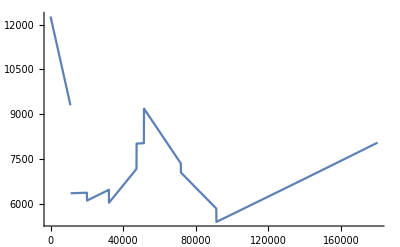

```mathematica
Plot[(p[h]/p''''[h])^(1/4),{h,0,180000},PlotRange->Full]
```

## RSS v6 model (Starwaster, 2014-03-17, in commit ).

```mathematica
rssString="key =	0	1.00074938005159	0	-0.112932216731154
			key =	1	0.887817163320432	-0.112932216731154	-0.102383696800236
			key =	2	0.785433466520196	-0.102383696800236	-0.092606079428248
			key =	3	0.692827387091948	-0.092606079428248	-0.083559421640834
			key =	4	0.609267965451115	-0.083559421640834	-0.075204960098835
			key =	5	0.53406300535228	-0.075204960098835	-0.067505103824342
			key =	6	0.466557901527938	-0.067505103824342	-0.060423426793117
			key =	7	0.406134474734821	-0.060423426793117	-0.053924660387524
			key =	8	0.352209814347297	-0.053924660387524	-0.047974685703597
			key =	9	0.3042351286437	-0.047974685703597	-0.042540525705509
			key =	10	0.261694602938191	-0.042540525705509	-0.037590337220107
			key =	11	0.224104265718084	-0.037590337220107	-0.032471289833586
			key =	12	0.191632975884499	-0.032471289833586	-0.027843493592706
			key =	13	0.163789482291792	-0.027843493592706	-0.02379794698535
			key =	14	0.139991535306442	-0.02379794698535	-0.020340201879907
			key =	15	0.119651333426536	-0.020340201879907	-0.017384853103928
			key =	16	0.102266480322608	-0.017384853103928	-0.014858904509876
			key =	17	0.087407575812732	-0.014858904509876	-0.012699965994175
			key =	18	0.074707609818557	-0.012699965994175	-0.010854712482068
			key =	19	0.063852897336488	-0.010854712482068	-0.009277566815723
			key =	20	0.054575330520766	-0.009277566815723	-0.005936489407756
			key =	25	0.024892883481984	-0.005936489407756	-0.002686584679796
			key =	30	0.011459960083005	-0.002686584679796	-0.001167830800293
			key =	35	0.005620806081539	-0.001167830800293	-0.00040944307168
			key =	45	0.001526375364736	-0.00040944307168	-0.000105243424372
			key =	55	0.00047394112102	-0.000105243424372	-0.00003098333627
			key =	65	0.000164107758324	-0.00003098333627	-0.00001019066441
			key =	75	0.000062201114229	-0.00001019066441	-0.000003675860762
			key =	85	0.000025442506612	-0.000003675860762	-0.000001196261407
			key =	100	0.000007498585506	-0.000001196261407	-0.000000394672641
			key =	110	0.0000035518591	-0.000000394672641	-0.000000179020197
			key =	120	0.000001761657127	-0.000000179020197	-0.000000085162644
			key =	130	0.000000910030685	-0.000000085162644	-0.00000004225905
			key =	140	0.000000487440187	-0.00000004225905	-0.000000021773993
			key =	150	0.000000269700262	-0.000000021773993	-0.000000011604662
			key =	160	0.000000153653645	-0.000000011604662	-0.000000006376405
			key =	170	0.000000089889599	-0.000000006376405	-0.00000000898896
			key =	180	0	-0.00000000898896	0";
```

```mathematica
rssRaw=ToExpression["{"~~StringReplace[rssString,{"\n"->"},\n","\t\t\t"->"","\t"->",","key =\t"->"{"}]~~"}}"];
```

```mathematica
xL=1000rssRawᵀ⟦1⟧;
yL=rssRawᵀ⟦2⟧*atm;
tgLin=rssRawᵀ⟦3⟧*atm/km;
tgLout=rssRawᵀ⟦4⟧*atm/km;
```

## Spline computations.

### Computation (piecewise best approximation cubic interpolating, cubic Hermite interpolating).

```mathematica
ε=1*^-6;
```

```mathematica
100(bounds ⟦2;;⟧-bounds⟦;;-2⟧)/bounds⟦-1⟧//Round
```

{6,5,7,8,2,11,8,3,49}

```mathematica
stepCounts={4,5,7,9,2,9,9,4,51};
stepCounts//Total
```

100

```mathematica
Quiet[
xxH=Table[
steps[pLayers⟦i⟧,bounds⟦i⟧,bounds⟦i+1⟧,stepCounts⟦i⟧],
{i,1,Length[pLayers]}
];
]
polyH=Table[
bestContinuousInterpolatingPiecewiseCubic[
pLayers⟦i⟧,xxH⟦i⟧,h,ε],
{i,1,Length[pLayers]}
];
dPolyH=D[polyH,h];
tgHin=Prepend[Join@@Table[
Table[dPolyH⟦i,j-1⟧/.h->xxH⟦i,j⟧,{j,2,Length[xxH⟦i⟧]}],
{i,1,Length[pLayers]}
],p'[xxH⟦1,1⟧]];
tgHout=Append[Join@@Table[
Table[dPolyH⟦i,j⟧/.h->xxH⟦i,j⟧,{j,1,Length[xxH⟦i⟧]-1}],
{i,1,Length[pLayers]}
],p'[xxH⟦-1,-1⟧]];
xH=Append[Union@@xxH⟦;;,;;-2⟧,xxH⟦-1,-1⟧];
yH=p/@xH;
tgH=p'/@xH;
```

```mathematica
stepCountsHH={8,11,15,18,4,19,17,7,101};
```

```mathematica
Quiet[
xxHH=Table[
steps[pLayers⟦i⟧,bounds⟦i⟧,bounds⟦i+1⟧,stepCountsHH⟦i⟧],
{i,1,Length[pLayers]}
];
]
polyHH=Table[
bestContinuousInterpolatingPiecewiseCubic[
pLayers⟦i⟧,xxHH⟦i⟧,h,ε],
{i,1,Length[pLayers]}
];
dPolyHH=D[polyHH,h];
tgHHin=Prepend[Join@@Table[
Table[dPolyHH⟦i,j-1⟧/.h->xxHH⟦i,j⟧,{j,2,Length[xxHH⟦i⟧]}],
{i,1,Length[pLayers]}
],p'[xxHH⟦1,1⟧]];
tgHHout=Append[Join@@Table[
Table[dPolyHH⟦i,j⟧/.h->xxHH⟦i,j⟧,{j,1,Length[xxHH⟦i⟧]-1}],
{i,1,Length[pLayers]}
],p'[xxHH⟦-1,-1⟧]];
xHH=Append[Union@@xxHH⟦;;,;;-2⟧,xxHH⟦-1,-1⟧];
yHH=p/@xHH;
tgHH=p'/@xHH;
```

## Error plots.

Colouring:
Piecewise Hermite interpolation (100 points),
Piecewise best approximation (100 points),
Piecewise Hermite interpolation (200 points),
Piecewise best approximation (200 points),
RSS v6.

### Relative error plots.

#### Logarithmic magnitude of the relative error.

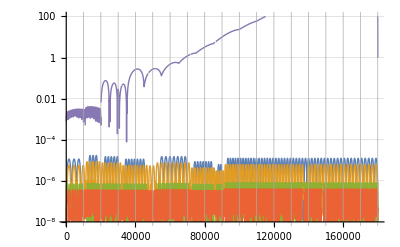

```mathematica
LogPlot[{
Abs[(approximation[xH,yH,tgH,tgH][h])/p[h]-1],
Abs[(approximation[xH,yH,tgHout,tgHin][h])/p[h]-1],
Abs[(approximation[xHH,yHH,tgHH,tgHH][h])/p[h]-1],
Abs[(approximation[xHH,yHH,tgHHout,tgHHin][h])/p[h]-1],

Abs[(approximation[xL,yL,tgLout,tgLin][h])/p[h]-1]},
{h,0,Last[xH]},PlotRange->{1*^-8,100},PlotStyle->Thick,
ImageSize->Full,Ticks->{Range[0,190km,10000],10.^Range[-13,2]},
GridLines->{Range[0,190km,10km],Flatten@Outer[Times,10.^Range[-13,2],Range[1,9,1]]},
GridLinesStyle->Lighter@Gray
]
```

#### A closer look at the troposphere and stratosphere, where the RSS v6 model isn’t completely insane.

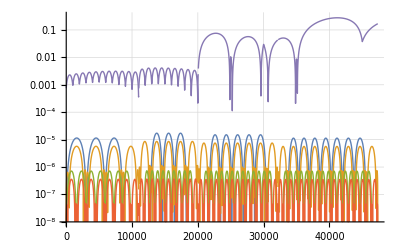

```mathematica
LogPlot[{
Abs[(approximation[xH,yH,tgH,tgH][h])/p[h]-1],
Abs[(approximation[xH,yH,tgHout,tgHin][h])/p[h]-1],
Abs[(approximation[xHH,yHH,tgHH,tgHH][h])/p[h]-1],
Abs[(approximation[xHH,yHH,tgHHout,tgHHin][h])/p[h]-1],

Abs[(approximation[xL,yL,tgLout,tgLin][h])/p[h]-1]},
{h,0,47349.303740712574},PlotRange->{1*^-8,.31},PlotStyle->Thick,
ImageSize->Full,Ticks->{Range[0,xH⟦-1⟧,1000],10.^Range[-13,2]},
GridLines->{Range[0,xH⟦-1⟧,1000],Flatten@Outer[Times,10.^Range[-13,2],Range[1,9,1]]},
GridLinesStyle->Lighter@Gray
]
```

#### Magnitude of the relative error.

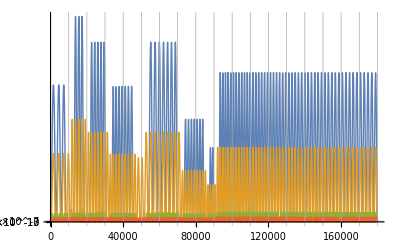

```mathematica
Plot[{
Abs[(approximation[xH,yH,tgH,tgH][h])/p[h]-1],
Abs[(approximation[xH,yH,tgHout,tgHin][h])/p[h]-1],
Abs[(approximation[xHH,yHH,tgHH,tgHH][h])/p[h]-1],
Abs[(approximation[xHH,yHH,tgHHout,tgHHin][h])/p[h]-1]},
{h,0,xH//Last},PlotStyle->Thick,
ImageSize->Full,Ticks->{Range[0,180km,10000],10.^Range[-13,2]},
GridLines->{Range[0,180km,10000],Flatten@Outer[Times,10.^Range[-13,2],Range[1,9,1]]},
GridLinesStyle->Lighter@Gray,ClippingStyle->Red
]
```

#### Magnitude of the relative error (100-step and 200-step, side by side)

200 points allows us to better even out the errors between the exponential chunks of the ISA model.

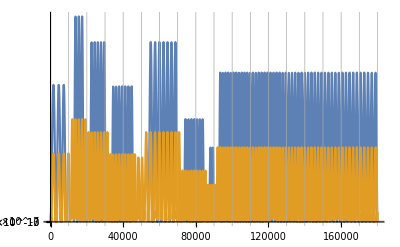
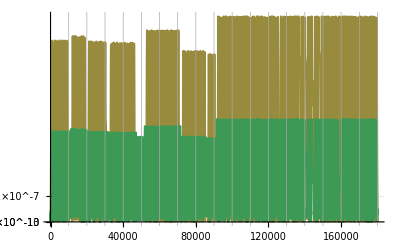

```mathematica
Row[{
Plot[{
Abs[(approximation[xH,yH,tgH,tgH][h])/p[h]-1],
Abs[(approximation[xH,yH,tgHout,tgHin][h])/p[h]-1]},
{h,0,xH//Last},PlotStyle->Thick,
ImageSize->Scaled[.4],Ticks->{Range[0,180km,10000],10.^Range[-13,2]},
GridLines->{Range[0,180km,10000],Flatten@Outer[Times,10.^Range[-13,2],Range[1,9,1]]},
GridLinesStyle->Lighter@Gray,ClippingStyle->Red
],
Plot[{
Abs[(approximation[xHH,yHH,tgHH,tgHH][h])/p[h]-1],
Abs[1/p[h] approximation[xHH,yHH,tgHHout,tgHHin][h]-1]},
{h,0,xH//Last},PlotStyle->{{Thick,ColorData[1][3]},{ColorData[1][4]}},
ImageSize->Scaled[.4],Ticks->{Range[0,180km,10000],10.^Range[-13,2]},
GridLines->{Range[0,180km,10000],Flatten@Outer[Times,10.^Range[-13,2],Range[1,9,1]]},
GridLinesStyle->Lighter@Gray,ClippingStyle->Red
]}]
```

#### Relative error.

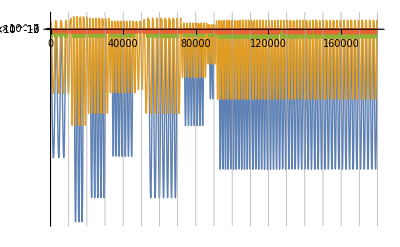

```mathematica
Plot[{
(approximation[xH,yH,tgH,tgH][h])/p[h]-1,
(approximation[xH,yH,tgHout,tgHin][h])/p[h]-1,
(approximation[xHH,yHH,tgHH,tgHH][h])/p[h]-1,
(approximation[xHH,yHH,tgHHout,tgHHin][h])/p[h]-1},
{h,0,xH//Last},PlotStyle->{Thick},
ImageSize->Full,Ticks->{Range[0,180km,10000],Flatten[{#,-#}&/@(10.^Range[-13,2])]},
GridLines->{Range[0,180km,10000],Flatten[{#,-#}&/@Outer[Times,10.^Range[-13,2],Range[1,9,1]]]},
GridLinesStyle->Lighter@Gray,ClippingStyle->Red
]
```

### Absolute error plots.

#### Logarithmic magnitude of the absolute error.

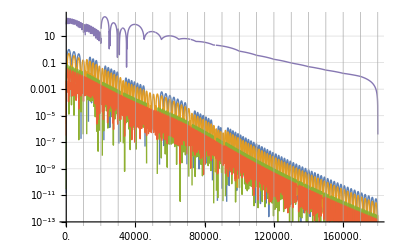

```mathematica
LogPlot[{
Abs[approximation[xH,yH,tgH,tgH][h]-p[h]],
Abs[approximation[xH,yH,tgHout,tgHin][h]-p[h]],
Abs[approximation[xHH,yHH,tgHH,tgHH][h]-p[h]],
Abs[approximation[xHH,yHH,tgHHout,tgHHin][h]-p[h]],
Abs[approximation[xL,yL,tgLout,tgLin][h]-p[h]]},
{h,First[xH],Last[xH]},PlotRange->{1*^-13,300},PlotStyle->{Thick},
ImageSize->Full,Ticks->{Range[0,180km,10km],Flatten[{#,-#}&/@(10.^Range[-13,2])]},
GridLines->{Range[0,180km,10km],Flatten[{#,-#}&/@Outer[Times,10.^Range[-13,2],Range[1,9,1]]]},
GridLinesStyle->Lighter@Gray
]
```

## Output.

### Pressure keyframes for the RSS configuration file.

```mathematica
keyFrames[xHH/km,yHH/atm,tgHHin/(atm/km),tgHHout/(atm/km)]
```

key =   0.                   1.                        -0.11856045370921518       -0.11855959978771942
key =   1.5512810696042834   0.8293033334108524        -0.10183830225110932       -0.10183674646034666
key =   3.049490512617914    0.6877017510446373        -0.08747110450514875       -0.08746976950185438
key =   4.496387604836978    0.5702444163147664        -0.0751284129344817        -0.07512726633490288
key =   5.893677091578151    0.47282126627696414       -0.06452535720588375       -0.06452437241824793
key =   7.243010623061255    0.3920205567378669        -0.05541708242752019       -0.05541623726573463
key =   8.545988169576226    0.3250104789672165        -0.047593141263616516      -0.047592415333238956
key =   9.804159415369073    0.26944079326066694       -0.040872666060624986      -0.040872042882559356
key =   11.01902513031035    0.2233611050921582        -0.035100221317578735      -0.035099557970493446
key =   11.84014685339708    0.19632505252876972       -0.03084380270879462       -0.03084310345055893
key =   12.661479569463696   0.17256150402323664       -0.02710343581969091       -0.027102821588632576
key =   13.483023359760763   0.1516743473174663        -0.023816656413559647      -0.023816116576602698
key =   14.304778305580532   0.1333154167235328        -0.020928458501624652      -0.020927984178645793
key =   15.12674448825698    0.1171786895168694        -0.018390506878715605      -0.018390090023457557
key =   15.948921989165822   0.10299518481855771       -0.016160327709296325      -0.01615996154844787
key =   16.771310889724543   0.09052847993471885       -0.014200598194339229      -0.014200276408409946
key =   17.593911271392436   0.07957076941364262       -0.012478521248672299      -0.012478238370883084
key =   18.416723215670608   0.06993940112805067       -0.010965277100050496      -0.010965028558431775
key =   19.239746804102023   0.06147383164159355       -0.00963554111113529       -0.00963532275380243
key =   20.062982118274434   0.05403295010784879       -0.008467059560467996      -0.008466865633093621
key =   20.848089497565947   0.04778939820639058       -0.007459985030116664      -0.007459812291011911
key =   21.63620936661535    0.042267349078245586      -0.0065726934531660074     -0.00657254126906443
key =   22.42735394519108    0.037383419911108245      -0.00579093891910887       -0.0057908050878031645
key =   23.221535507546527   0.03306386499304308       -0.0051021685425771636     -0.00510205025182942
key =   24.018766382699184   0.029243461811422816      -0.0044953216976765225     -0.00449521773683876
key =   24.8190589547115     0.025864525910496747      -0.003960654553978478      -0.0039605627357514476
key =   25.622425662973434   0.022876039623080074      -0.0034895812227674168     -0.0034895006191361998
key =   26.42887900248672    0.02023288151260161       -0.0030745380406068013     -0.0030744671255894637
key =   27.238431524150865   0.017895144883579222      -0.0027088605245762457     -0.0027087978126772794
key =   28.05109583505088    0.01582753506445577       -0.0023866766401096145     -0.002386621463670356
key =   28.86688459874678    0.013998836357006461      -0.00210281336829757       -0.002102764823022757
key =   29.685810535564812   0.012381440599191202      -0.0018527126731341518     -0.0018526698042597327
key =   30.50788642289051    0.010950930219291178      -0.0016323587220781594     -0.0016323209889605624
key =   31.333125095463508   0.009685709482500008      -0.001438213440182944      -0.0014381801209664721
key =   32.16153944567676    0.00856667835929167       -0.001267159475800941      -0.0012671291433869782
key =   32.938227246035915   0.007641143253424154      -0.0011194443454613022     -0.001119416715203487
key =   33.72239861830024    0.006815621618893492      -0.00098894869315807       -0.0009889242507575187
key =   34.514127125411996   0.00607930403304661       -0.0008736658458577912     -0.0008736442823188312
key =   35.31348708126911    0.005422549546182163      -0.0007718223103765099     -0.0007718032220685227
key =   36.12055355892001    0.004836759353067881      -0.0006818512473742133     -0.0006818343999548707
key =   36.93540239885774    0.004314264124281222      -0.000602368599707903      -0.0006023537275719138
key =   37.758110217414796   0.0038482235201537335     -0.0005321516055926249     -0.0005321384600078337
key =   38.588754415260034   0.0034325365698691804     -0.00047012007111754727    -0.00047010846628046477
key =   39.42741318599914    0.003061761740754522      -0.0004153197608027341     -0.0004153094957067317
key =   40.274165524880075   0.002731045649879268      -0.0003669076453724236     -0.0003668985815476719
key =   41.12909123760493    0.0024360594834088893     -0.00032413902137201937    -0.00032413101651729585
key =   41.992270949249814   0.0021729422902310026     -0.0002863559791165239     -0.0002863489027220139
key =   42.86378611329412    0.0019382504065130982     -0.00025297731542709285    -0.0002529710682454082
key =   43.74371902076092    0.0017289123482408188     -0.00022348959544633097    -0.00022348406691727552
key =   44.63215280946986    0.001542188580481708      -0.00019743921339973302    -0.00019743433762356509
key =   45.52917147340433    0.0013756356360598086     -0.00017442548188152307    -0.0001744211709807741
key =   46.434859872194416   0.0012270741133522903     -0.0001540943976740258     -0.00015409058835020637
key =   47.34930374071258    0.0010945601337771134     -0.0001361332366854071     -0.0001361300999622217
key =   48.364384412817486   0.0009647618356676518     -0.00011995173663077706    -0.0001199491828070985
key =   49.379785586778326   0.0008503557210569973     -0.00010569384206786046    -0.00010569159114107088
key =   50.39550741421541    0.0007495164938529389     -0.00009313069365486576    -0.00009312871041255892
key =   51.41155004684329    0.0006606353132858362     -0.00008206084867257565    -0.00008205914602801715
key =   52.60233679755664    0.0005693036016959514     -0.00007155713957078758    -0.00007155568678730067
key =   53.77919611346216    0.0004905938576126548     -0.00006239767385386734    -0.00006239640894781644
key =   54.94228410298658    0.0004227624006014844     -0.0000544104256104594     -0.000054409320819982295
key =   56.091755284696234   0.00036430633500513854    -0.00004744540325580311    -0.00004744444130583597
key =   57.22776259968469    0.0003139303145738763     -0.000041371807283236435   -0.00004137096802618017
key =   58.35045742395875    0.0002705178923931361     -0.00003607556860149402    -0.00003607483704626997
key =   59.45998958082039    0.00023310682382008942    -0.00003145721292357758    -0.00003145657516845965
key =   60.556507353241216   0.00020086777728288698    -0.000027429992203311256   -0.000027429435582640572
key =   61.64015749622714    0.00017308598293538365    -0.000023918256528569814   -0.000023917771478660894
key =   62.711085249170246   0.00014914541394851294    -0.00002085603677190657    -0.000020855613696683044
key =   63.76943434818539    0.00012851515108212665    -0.00001818580287864788    -0.00001818543442226444
key =   64.815347038429      0.00011073762934697615    -0.000015857387455682573   -0.000015857065686591502
key =   65.84896408639746    0.00009541850709542147    -0.000013827041357366145   -0.000013826760859805913
key =   66.8704247922031     0.00008221793368536839    -0.000012056614537032086   -0.000012056370038392204
key =   67.87986700182476    0.00007084302273310274    -0.000010512838560751086   -0.000010512625468395554
key =   68.8774271193317     0.00006104136458678227    -9.166702602146737e-6      -9.16651697825816e-6
key =   69.86324011907763    0.000052595434599546184   -7.992908453558665e-6      -7.99274660841423e-6
key =   70.8374395578637     0.00004531777356493782    -6.969395258678345e-6      -6.969253895473243e-6
key =   71.80015758707647    0.000039046833733439246   -6.076925603873962e-6      -6.076804772790693e-6
key =   72.68865461815959    0.00003398575432010344    -5.330948534717209e-6      -5.330845145916447e-6
key =   73.57022854353788    0.000029580547160393628   -4.676538578623587e-6      -4.676447927603061e-6
key =   74.44493098881618    0.000025746233592392944   -4.102454926858646e-6      -4.102375481234327e-6
key =   75.31281323119997    0.000022408843008637936   -3.5988387258317427e-6     -3.598768870482683e-6
key =   76.17392620126307    0.00001950398719402563    -3.1570408681075038e-6     -3.1569798751603056e-6
key =   77.02832048471646    0.00001697561926004407    -2.7694742556909047e-6     -2.769420486182663e-6
key =   77.87604632417766    0.000014774953279356489   -2.429482135652753e-6      -2.4294350158398353e-6
key =   78.71715362094046    0.00001285952381730844    -2.1312254357726504e-6     -2.1311841056792775e-6
key =   79.551691936745      0.000011192367249356912   -1.8695813146192711e-6     -1.8695450373390193e-6
key =   80.37971049554787    9.741309097476518e-6      -1.6400558045349966e-6     -1.6400240307869246e-6
key =   81.20125818529202    8.478343659349097e-6      -1.4387065426054444e-6     -1.4386785891349887e-6
key =   82.01638355967633    7.379093980827345e-6      -1.2620747763849974e-6     -1.2620502652020841e-6
key =   82.82513483992473    6.422341768933253e-6      -1.1071265718097054e-6     -1.1071051142141048e-6
key =   83.62755991655452    5.589618189260209e-6      -9.712002904574998e-7      -9.71181448483281e-7
key =   84.42370635114384    4.864847663982511e-6      -8.519608581116953e-7      -8.51944338109559e-7
key =   85.2136213780981     4.234037807288761e-6      -7.473599370498319e-7      -7.473454667471942e-7
key =   85.99735190641914    3.6850095235747807e-6     -6.556005771082963e-7      -6.55587954868776e-7
key =   86.77126507788661    3.2092787757787186e-6     -5.754642912975324e-7      -5.75453268314719e-7
key =   87.53914411678717    2.794954292752292e-6      -5.051226323794921e-7      -5.051129705129523e-7
key =   88.30103431720043    2.4341112574484694e-6     -4.4337850910771023e-7     -4.4337003053471976e-7
key =   89.05698066083089    2.119847408523293e-6      -3.8918117164669293e-7     -3.8917373913668035e-7
key =   89.80702781872314    1.846151123042689e-6      -3.4160827520346016e-7     -3.416017290173781e-7
key =   90.55122015297522    1.6077865140798708e-6     -2.998501678608832e-7      -2.9984441920604384e-7
key =   91.28960171845002    1.4001933490614182e-6     -2.6319616869285707e-7     -2.486952005932888e-7
key =   92.00550873461046    1.2333118599412074e-6     -2.1819956067829382e-7     -2.1819399765406504e-7
key =   92.72423273172485    1.0863213945314536e-6     -1.9143856792449206e-7     -1.9143367699672882e-7
key =   93.44578535382313    9.568509390520772e-7      -1.6795972868642057e-7     -1.679554483744513e-7
key =   94.17017829735393    8.428121226896023e-7      -1.4736050239941215e-7     -1.473567449209859e-7
key =   94.89742331145317    7.423655223488129e-7      -1.2928769638390706e-7     -1.2928439701265594e-7
key =   95.62753219821417    6.538909846164284e-7      -1.1343144740828045e-7     -1.134285511429241e-7
key =   96.3605168129594     5.759614859695728e-7      -9.951989504709977e-8      -9.95173584899587e-8
key =   97.09638906451391    5.073201093718896e-7      -8.731453760845615e-8      -8.73123057928803e-8
key =   97.83516091548039    4.46859765699811e-7       -7.660609906427105e-8      -7.660414409027002e-8
key =   98.57684438251582    3.936053327437919e-7      -6.721099425878047e-8      -6.720928192049638e-8
key =   99.32145153660994    3.466979235488415e-7      -5.896815235791663e-8      -5.8966646584020774e-8
key =   100.0689945033653    3.053810302255262e-7      -5.1736241448129367e-8     -5.173491910923864e-8
key =   100.81948546327908   2.6898831963163175e-7     -4.539127656936708e-8      -4.5390118869270026e-8
key =   101.57293665202647   2.3693288398456065e-7     -3.982448055650987e-8      -3.982346454334898e-8
key =   102.32936036074604   2.0869777294549137e-7     -3.4940411954074005e-8     -3.493952204123044e-8
key =   103.08876893632655   1.838276543975248e-7      -3.06553395600465e-8       -3.0654556031009224e-8
key =   103.85117478169572   1.6192146935538855e-7     -2.689579529450524e-8      -2.6895108609656207e-8
key =   104.61659035611073   1.426259624876361e-7      -2.3597329116220923e-8     -2.3596726899186627e-8
key =   105.38502817545033   1.2562998386281498e-7     -2.070339136635255e-8      -2.070286293924818e-8
key =   106.15650081250897   1.1065946997674138e-7     -1.8164369129178214e-8     -1.8163906411457024e-8
key =   106.9310208972926    9.747302307980794e-8      -1.593673553266452e-8      -1.593632957429027e-8
key =   107.70860111731623   8.585801747804816e-8      -1.3982299517997457e-8     -1.3981941938454638e-8
key =   108.4892542179035    7.562716998532403e-8      -1.2267554609866885e-8     -1.2267240569173477e-8
key =   109.27299300248785   6.661551919379164e-8      -1.076310461319652e-8      -1.0762830152965702e-8
key =   110.05983033291581   5.867776482658846e-8      -9.443159955895734e-9      -9.4429192202336e-9
key =   110.84977912975185   5.168592424694919e-8      -8.28509192107281e-9       -8.284880967146415e-9
key =   111.64285237258542   4.552726831549305e-8      -7.269047652113642e-9      -7.268861865960066e-9
key =   112.43906310033962   4.010250329483534e-8      -6.377608557329834e-9      -6.3774461283796e-9
key =   113.23842441158197   3.532416947066346e-8      -5.595493791526083e-9      -5.59535127707469e-9
key =   114.04094946483697   3.1115230655123596e-8     -4.9092955575989594e-9     -4.909170545557526e-9
key =   114.84665147890068   2.740783181815693e-8      -4.3072507109624235e-9     -4.3071406919610695e-9
key =   115.65554373315715   2.4142204805057678e-8     -3.7790381927874045e-9     -3.778941838062271e-9
key =   116.46763956789694   2.1265704487747348e-8     -3.315603840776064e-9      -3.315519144373566e-9
key =   117.28295238463754   1.8731959801643352e-8     -2.909002997779728e-9      -2.9089289141697117e-9
key =   118.10149564644574   1.6500125973500722e-8     -2.5522660046340328e-9     -2.552200839725792e-9
key =   118.92328287826211   1.4534225878138631e-8     -2.2392772678887408e-9     -2.239220082924367e-9
key =   119.74832766722746   1.2802569899865155e-8     -1.964671764606749e-9      -1.9646216869169834e-9
key =   120.57664366301124   1.1277244940900727e-8     -1.7237423517032067e-9     -1.7236984216421938e-9
key =   121.40824457814219   9.933664334603154e-9      -1.5123590509328848e-9     -1.5123204615818876e-9
key =   122.2431441883408    8.750171403809505e-9      -1.326898375254258e-9      -1.3268644348883113e-9
key =   123.08135633285417   7.707690270003333e-9      -1.1641812419707625e-9     -1.1641515388873978e-9
key =   123.92289491479256   6.7894182812367484e-9     -1.0214185504153104e-9     -1.021392572809208e-9
key =   124.7677739014685    5.980555098096755e-9      -8.961632199478459e-10     -8.961404106466935e-10
key =   125.61600732473762   5.268064068329123e-9      -7.862682022129306e-10     -7.862480762281916e-10
key =   126.46760928134195   4.640462041568822e-9      -6.898496745700762e-10     -6.898321179137454e-10
key =   127.32259393325515   4.087634234370453e-9      -6.052551118185885e-10     -6.052396439440843e-10
key =   128.18097550803      3.6006711597960495e-9     -5.310344061653454e-10     -5.310208297746401e-10
key =   129.0427682991481    3.171724991706807e-9      -4.659153750150121e-10     -4.659035126174821e-10
key =   129.90798666637178   2.7938830473793276e-9     -4.08781908703883e-10      -4.08771478024948e-10
key =   130.7766450360982    2.461056348167078e-9      -3.586546789530001e-10     -3.586455122851607e-10
key =   131.64875790171564   2.167881461118848e-9      -3.1467448386623625e-10    -3.1466643941650315e-10
key =   132.52433982396218   1.9096340386672714e-9     -2.760875109002025e-10     -2.7608048640960875e-10
key =   133.4034054312866    1.6821526621691311e-9     -2.422324130818198e-10     -2.422262147221923e-10
key =   134.28596942021136   1.4817717612582223e-9     -2.1252885851739006e-10    -2.1252344224971152e-10
key =   135.17204655569842   1.3052625273415275e-9     -1.8646778008939614e-10    -1.8646303431174026e-10
key =   136.06165167151667   1.149780868494151e-9      -1.6360249304130826e-10    -1.6359832895033542e-10
key =   136.9547996706124    1.0128215665635313e-9     -1.4354110044370613e-10    -1.4353742247124066e-10
key =   137.8515055254816    8.921778973149445e-10     -1.259397403316904e-10     -1.2593652233520667e-10
key =   138.75178427854485   7.859060625484956e-10     -1.104967631349645e-10     -1.1049393456194306e-10
key =   139.6556510425247    6.922938607161996e-10     -9.694747706774628e-11     -9.694500988836427e-11
key =   140.56312100082533   6.09833090916068e-10      -8.505967791134393e-11     -8.505750933931027e-11
key =   141.47420940791469   5.371952453424906e-10     -7.462961018742898e-11     -7.462769981656357e-11
key =   142.38893158970896   4.732100982986395e-10     -6.547851118042345e-11     -6.547684368617612e-11
key =   143.3073029439597    4.168468465829776e-10     -5.744955662281224e-11     -5.7448088486878884e-11
key =   144.22933894064346   3.671974972015254e-10     -5.040513169452915e-11     -5.040384756661839e-11
key =   145.15505512235356   3.234622345933982e-10     -4.4224515069882136e-11    -4.422338638786745e-11
key =   146.0844671046949    2.8493653147468415e-10    -3.88017761245299e-11      -3.880078803092987e-11
key =   147.017590576681     2.5099979551865794e-10    -3.404398566830358e-11     -3.404311651075543e-11
key =   147.9544413011336    2.2110536885300994e-10    -2.986959908335178e-11     -2.986883568628309e-11
key =   148.895035115085     1.9477171916586073e-10    -2.620707893071936e-11     -2.620640924310837e-11
key =   149.83938793018282   1.7157468042414262e-10    -2.2993658533612386e-11    -2.299307096473485e-11
key =   150.78751573309765   1.5114061812990165e-10    -2.0174266373207763e-11    -2.0173752650523618e-11
key =   151.73943458593294   1.3314040894531616e-10    -1.7700588075511552e-11    -1.7700135192555592e-11
key =   152.69516062663794   1.1728413764612875e-10    -1.5530227719501764e-11    -1.55298307087732e-11
key =   153.65471006942323   1.0331642592731239e-10    -1.3625993693520843e-11    -1.3625647313417621e-11
key =   154.61809920517865   9.101231777083398e-11     -1.195525487829176e-11     -1.1954949122579921e-11
key =   155.58534440189447   8.017365505741884e-11     -1.0489376555386223e-11    -1.0489108389627964e-11
key =   156.55646210508482   7.062588500703516e-11     -9.20323991640719e-12      -9.203005428364908e-12
key =   157.5314688382143    6.221524799385088e-11     -8.074805705209974e-12     -8.074599349924489e-12
key =   158.51038120312697   5.480630041286311e-11     -7.08473554143093e-12      -7.0845542538637285e-12
key =   159.49321588047854   4.8279732676118466e-11    -6.2160628033143375e-12    -6.2159047891625916e-12
key =   160.47998963017102   4.25304471736388e-11      -5.4539036270954505e-12    -5.453764557808936e-12
key =   161.47071929179063   3.7465865224365877e-11    -4.785196076386637e-12     -4.785073908810809e-12
key =   162.46542178504822   3.3004435733348155e-11    -4.1984815792356605e-12    -4.1983745283769796e-12
key =   163.46411411022274   2.9074321522450202e-11    -3.683706563091199e-12     -3.683612355030496e-12
key =   164.4668133486077    2.5612242165515882e-11    -3.2320494760803846e-12    -3.2319674105206833e-12
key =   165.4735366629604    2.2562454681306163e-11    -2.835771964959891e-12     -2.835699374640052e-12
key =   166.48430129795432   1.9875855659365853e-11    -2.4880826010150204e-12    -2.488018919485026e-12
key =   167.49912458063434   1.750919035102187e-11     -2.183023910081614e-12     -2.1829684215361883e-12
key =   168.5180239208751    1.542435598158708e-11     -1.915369291207526e-12     -1.915320261046157e-12
key =   169.54101681184216   1.3587788058277363e-11    -1.6805317497743288e-12    -1.680488922352042e-12
key =   170.5681208304566    1.1969919785852967e-11    -1.4744879599724844e-12    -1.4744501946593233e-12
key =   171.59935363786235   1.054470588013509e-11     -1.2937070494689333e-12    -1.2936740139551017e-12
key =   172.6347329798968    9.289203107288329e-12     -1.1350916457412244e-12    -1.1350626946869318e-12
key =   173.67427668756457   8.183200790861963e-12     -9.959239255491945e-13     -9.95898542977519e-13
key =   174.71800267751422   7.208895333755879e-12     -8.738194000657575e-13     -8.737970230998723e-13
key =   175.76592895251846   6.350603511516141e-12     -7.666857284216306e-13     -7.666662249939894e-13
key =   176.81807360195734   5.594509918095206e-12     -6.726875605074617e-13     -6.726704032825175e-13
key =   177.87445480230463   4.928444495506458e-12     -5.90214200234423e-13      -5.901990996152515e-13
key =   178.93509081761772   4.3416865635263965e-12    -5.178525832961848e-13     -5.178393603297526e-13
key =   180.00000000003055   3.8247921925719374e-12    -4.5436294962888906e-13    -4.543569202735762e-13

## Temperature spline

```mathematica
xT=bounds;
yT=T/@bounds;
tgTin=(Append[T/@bounds,15+Celsius0]-Prepend[T/@bounds,0])/(Append[bounds,∞]-Prepend[bounds,-∞]);
tgTout=(Append[T/@bounds,15+Celsius0]-Prepend[T/@bounds,0])/(Append[bounds,∞]-Prepend[bounds,-∞]);
```

```mathematica
stepCountsT={20,1,13,22,1,29,18,1,95};
stepCountsT//Total
```

200

```mathematica
constantLayers={2,5,8};
```

```mathematica
Quiet[
xxT=Table[
If[MemberQ[constantLayers,i],
{bounds⟦i⟧,bounds⟦i+1⟧},
steps[TLayers⟦i⟧,bounds⟦i⟧,bounds⟦i+1⟧,stepCountsT⟦i⟧,(Abs[#1[#2]/Derivative[2][#1][#2]]^(1/2)&)]
],{i,1,Length[TLayers]}
];
polyT=Table[
If[MemberQ[constantLayers,i],
{TLayers⟦i⟧+((TLayers⟦i⟧[bounds⟦i+1⟧]-TLayers⟦i⟧[bounds⟦i⟧])/(bounds⟦i+1⟧-bounds⟦i⟧))(h-bounds⟦i⟧)},
bestContinuousInterpolatingPiecewiseCubic[
TLayers⟦i⟧,xxT⟦i⟧,h,-.5(*This makes absolutely no sense. It gives a wonderful approximation. Honeybadger don't give a shit.*)]
],{i,1,Length[TLayers]}
];
]
dPolyT=D[polyT,h];
tgTin=Prepend[Join@@Table[
Table[dPolyT⟦i,j-1⟧/.h->xxT⟦i,j⟧,{j,2,Length[xxT⟦i⟧]}],
{i,1,Length[TLayers]}
],T'[xxT⟦1,1⟧]];
tgTout=Append[Join@@Table[
Table[dPolyT⟦i,j⟧/.h->xxT⟦i,j⟧,{j,1,Length[xxT⟦i⟧]-1}],
{i,1,Length[TLayers]}
],T'[xxT⟦-1,-1⟧]];
xT=Append[Union@@xxT⟦;;,;;-2⟧,xxT⟦-1,-1⟧];
yT=T/@xT;
tgT=T'/@xT;
```

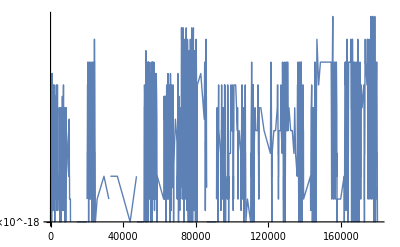

```mathematica
Plot[{
Abs[1/T[h] approximation[xT,yT,tgTout,tgTin][h]-1]},
{h,0,xT//Last},PlotStyle->Thick,
ImageSize->Full,Ticks->{Range[0,180km,10000],10.^Range[-18,30]},
GridLines->{Range[0,180km,10000],Flatten@Outer[Times,10.^Range[-18,30],Range[1,9,1]]},
GridLinesStyle->Lighter@Gray,ClippingStyle->Red
]
```

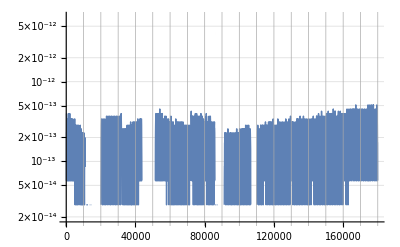

```mathematica
LogPlot[{
Abs[T[h]-approximation[xT,yT,tgTout,tgTin][h]]},
{h,0,xT//Last},PlotStyle->Thick,
ImageSize->Full,Ticks->{Range[0,180km,10000],10.^Range[-18,30]},
GridLines->{Range[0,180km,10000],Flatten@Outer[Times,10.^Range[-18,30],Range[1,9,1]]},
GridLinesStyle->Lighter@Gray,ClippingStyle->Red
]
```

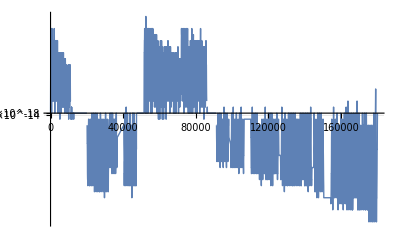

```mathematica
Plot[{
T[h]-approximation[xT,yT,tgTout,tgTin][h]},
{h,0,xT//Last},PlotStyle->Thick,
ImageSize->Full,Ticks->{Range[0,180km,10000],Flatten[{#,-#}&/@(10.^Range[-18,30])]},
GridLines->{Range[0,180km,10000],Flatten[{#,-#}&/@Outer[Times,10.^Range[-18,30],Range[1,9,1]]]},
GridLinesStyle->Lighter@Gray,ClippingStyle->Red
]
```

```mathematica
keyFrames[xT/km,yT-Celsius0,tgTin/(1/km),tgTout/(1/km)]
```

key =   0.                   15.                    -6.5                  -6.500000000001275
key =   0.5873532661402939   11.182555706237338     -6.498801675418761    -6.4988016754213
key =   1.1708835840211225   7.3906551726050225     -6.497611478581974    -6.497611478584431
key =   1.7505894467842473   3.624294347296768      -6.49642940601396     -6.496429406016377
key =   2.326469355432374    -0.11653078269370098   -6.495255454267846    -6.495255454270236
key =   2.8985218188122817   -3.8318241914215605    -6.494089619924352    -6.494089619926598
key =   3.4667453535972417   -7.521589813835249     -6.492931899591555    -6.492931899593788
key =   4.031138484268703    -11.185831545616793    -6.491782289905223    -6.491782289907498
key =   4.591699743097215    -14.824553243017135    -6.490640787528829    -6.490640787531016
key =   5.148427670122567    -18.437758722686567    -6.489507389153364    -6.489507389155518
key =   5.701320813133119    -22.02545176150059     -6.488382091497568    -6.488382091499679
key =   6.250377727644286    -25.587636096380322    -6.487264891307991    -6.487264891310026
key =   6.795596976876166    -29.124315424107493    -6.486155785358754    -6.486155785360818
key =   7.336977131730267    -32.63549340113431     -6.485054770452147    -6.485054770454131
key =   7.874516770765299    -36.121173643387124    -6.483961843418107    -6.483961843420021
key =   8.408214480172017    -39.581359726064505    -6.48287700111461     -6.482877001116446
key =   8.93806885374706     -43.016055183428875    -6.481800240427441    -6.481800240429314
key =   9.464078492865767    -46.42526350859214     -6.4807315582707075   -6.480731558272612
key =   9.986242006453917    -49.80898815329434     -6.4796709515865105   -6.479670951588268
key =   10.504558010958375   -53.167232527675424    -6.478618417344989    -6.478618417346778
key =   11.01902513031035    -56.5                  -6.477573952544683    0.
key =   20.062982118274434   -56.5                  0.                    0.9937314143502549
key =   20.98084654897413    -55.5880202565871      0.9934460430471843    0.9934460430486778
key =   21.9008389620091     -54.67418896100597     0.993160133474848     0.9931601334763598
key =   22.8229605287171     -53.75850666193023     0.9928736860535489    0.9928736860550454
key =   23.747212423371924   -52.84097390917117     0.9925867012057574    0.9925867012072662
key =   24.673595823186716   -51.92159125367721     0.9922991793547712    0.9922991793562667
key =   25.602111908317323   -51.000359247533595    0.9920111209245535    0.9920111209260991
key =   26.53276186186562    -50.07727844396172     0.991722526339964     0.991722526341486
key =   27.46554686988287    -49.15234939731894     0.991433396026512     0.9914333960280677
key =   28.400468121373088   -48.22557266309792     0.9911437304104889    0.9911437304120656
key =   29.337526808296396   -47.296948797926234    0.9908535299190327    0.9908535299205682
key =   30.27672412557241    -46.36647835956603     0.9905627949798753    0.9905627949814342
key =   31.218061271083617   -45.4341619069134      0.9902715260216226    0.9902715260232213
key =   32.16153944567676    -44.5                  0.989979723473627     2.7719432257291707
key =   32.82294660742017    -42.666806255917464    2.771370665910895     2.7713706659124697
key =   33.48710277233055    -40.82637421834721     2.770795904853725     2.770795904855297
key =   34.154009078612766   -38.97870535550513     2.7702189437178615    2.7702189437193816
key =   34.823666669121195   -37.12380114207147     2.7696397836696485    2.7696397836711406
key =   35.496076691365815   -35.26166305918406     2.7690584258798556    2.7690584258814734
key =   36.17124029751821    -33.39229259443138     2.7684748715240217    2.7684748715256706
key =   36.84915864441759    -31.5156912418461      2.7678891217824617    2.7678891217840906
key =   37.529832893576796   -29.63186050189853     2.767301177839463     2.767301177841124
key =   38.213264211188296   -27.74080188148986     2.76671104088457      2.766711040886184
key =   38.899453768130186   -25.842516893946026    2.7661187121113655    2.766118712113003
key =   39.58840273997215    -23.93700705901128     2.765524192718115     2.765524192719894
key =   40.28011230698143    -22.024273902841713    2.7649274839079236    2.7649274839096822
key =   40.97458365412876    -20.104318957999368    2.7643285868881398    2.764328586889976
key =   41.67181797109436    -18.177143763445997    2.7637275028705144    2.7637275028724084
key =   42.37181645227385    -16.242749864536734    2.7631242330721166    2.763124233073838
key =   43.07458029678417    -14.301138813014575    2.7625187787134746    2.7625187787152146
key =   43.78011070846955    -12.352312167004072    2.761911141020266     2.7619111410220043
key =   44.48840889590738    -10.396271491005507    2.7613013212228212    2.761301321224471
key =   45.19947607241417    -8.43301835588943      2.7606893205553655    2.7606893205572822
key =   45.91331345605142    -6.4625543388903       2.7600751402573596    2.76007514025926
key =   46.629922269631564   -4.484881023601417     2.7594587815723663    2.759458781574291
key =   47.34930374071258    -2.5                   2.7588402457484524    0.
key =   51.41155004684329    -2.5                   0.                    -2.7553513604581865
key =   52.15213108353106    -4.540325693286491     -2.754716021161932    -2.754716021163976
key =   52.89004297885337    -6.5728299133947985    -2.7540831902420386   -2.7540831902440908
key =   53.625284454668574   -8.597514369303667     -2.7534528663253943   -2.7534528663274473
key =   54.35785423699868    -10.614380762784776    -2.7528250480464265   -2.7528250480483933
key =   55.08775105603217    -12.623430788399048    -2.752199734045201    -2.752199734047256
key =   55.81497364612668    -14.62466613349386     -2.751576922967658    -2.7515769229696683
key =   56.53952074581175    -16.618088478199184    -2.750956613465388    -2.750956613467415
key =   57.26139109779142    -18.60369949542431     -2.750338804195627    -2.750338804197677
key =   57.98058344894684    -20.58150085085441     -2.749723493821375    -2.749723493823433
key =   58.69709655033888    -22.55149420294663     -2.7491106810114005   -2.749110681013332
key =   59.41092915721056    -24.51368120292659     -2.74850036444002     -2.7485003644419135
key =   60.122080028989615   -26.46806349478453     -2.747892542787325    -2.7478925427890895
key =   60.83054792929086    -28.414642715271185    -2.7472872147390213   -2.7472872147407545
key =   61.536331625918585   -30.353420493894077    -2.7466843789866857   -2.7466843789884616
key =   62.2394298908689     -32.284398452913365    -2.746084034227258    -2.7460840342290855
key =   62.93984150033201    -34.20757820733763     -2.745486179164041    -2.7454861791656917
key =   63.637565234694456   -36.12296136491932     -2.744890812504956    -2.744890812506688
key =   64.33259987854133    -38.03054952615099     -2.7442979329646917   -2.7442979329663535
key =   65.02494422065837    -39.930344284260286    -2.7437075392629673   -2.743707539264589
key =   65.71459705403412    -41.82234722520562     -2.743119630125289    -2.7431196301269045
key =   66.40155717586185    -43.706559927671464    -2.7425342042830123   -2.742534204284564
key =   67.0858233875417     -45.58298396306344     -2.7419512604729457   -2.7419512604745284
key =   67.76739449468249    -47.45162089550365     -2.7413707974378      -2.741370797439288
key =   68.44626930710369    -49.31247228182542     -2.740792813925796    -2.740792813927293
key =   69.12244663883719    -51.165539671568524    -2.7402173086908177   -2.7402173086923263
key =   69.79592530812911    -53.010824606973586    -2.7396442804924463   -2.73964428049409
key =   70.46670413744148    -54.848328622976965    -2.739073728095952    -2.7390737280975683
key =   71.13478195345398    -56.6780532472053      -2.7385056502725837   -2.7385056502741403
key =   71.80015758707647    -58.5                  -2.7379400457984966   -1.9556714612861485
key =   72.61330146122056    -60.09004159019099     -1.9551779059965935   -1.955177905998404
key =   73.4235813878142     -61.67408380840237     -1.954686274873386    -1.9546862748752316
key =   74.2309958642791     -63.252128092591676    -1.9541965667661132   -1.9541965667679806
key =   75.0355433928183     -64.82417587481251     -1.9537087805307751   -1.9537087805326687
key =   75.8372224804201     -66.39022858121263     -1.953222915028312    -1.9532229150302491
key =   76.636031638862      -67.9502876320322      -1.9527389691243044   -1.952738969126156
key =   77.4319693847145     -69.50435444160118     -1.9522569416888984   -1.9522569416907407
key =   78.225034239345      -71.05243041833751     -1.9517768315970925   -1.9517768315988748
key =   79.01522472892147    -72.59451696474463     -1.9512986377285217   -1.951298637730309
key =   79.80253938441622    -74.13061547740938     -1.9508223589675013   -1.9508223589692886
key =   80.5869767416096     -75.66072734699961     -1.9503479942032356   -1.9503479942049349
key =   81.3685353410936     -77.1848539582615      -1.9498755423292158   -1.9498755423309364
key =   82.14721372827546    -78.70299669001744     -1.9494050022441314   -1.9494050022458285
key =   82.92301045338111    -80.21515691516328     -1.9489363728509024   -1.9489363728525333
key =   83.69592407145879    -81.72133600066562     -1.9484696530575316   -1.9484696530591166
key =   84.46595314238239    -83.22153530755938     -1.9480048417763363   -1.9480048417779692
key =   85.23309623085487    -84.71575619094494     -1.9475419379246102   -1.947541937926204
key =   85.99735190641914    -86.20400000000001     -1.9470809404241889   0.
key =   91.28960171845002    -86.20400000000001     0.                    0.9719465761506371
key =   92.12832386178835    -85.38891267215413     0.9716943332586346    0.9716943332596507
key =   92.96903608064213    -84.5721036221104      0.9714415903904057    0.9714415903914314
key =   93.81173937133609    -83.7535733082683      0.971188347894607     0.9711883478956649
key =   94.65643473272092    -82.93332219002036     0.9709346061216326    0.9709346061227379
key =   95.50312316617602    -82.11135072775184     0.9706803654225292    0.9706803654236148
key =   96.35180567561207    -81.28765938284019     0.9704256261490406    0.9704256261500883
key =   97.20248326747372    -80.46224861765484     0.9701703886534438    0.9701703886545137
key =   98.05515695074233    -79.6351188955567      0.9699146532888443    0.9699146532898968
key =   98.90982773693857    -78.80627068089782     0.969658420408929     0.9696584204099923
key =   99.76649664012515    -77.97570443902097     0.9694016903681137    0.9694016903692266
key =   100.62516467690959   -77.14342063625926     0.9691444635214075    0.969144463522557
key =   101.48583286644673   -76.30941973993583     0.9688867402245519    0.9688867402256827
key =   102.34850223044162   -75.47370221836343     0.968628520833918     0.9686285208350608
key =   103.21317379315218   -74.6362685408439      0.9683698057065883    0.9683698057076587
key =   104.0798485813919    -73.7971191776681      0.9681105952001697    0.9681105952013114
key =   104.94852762453256   -72.95625460011516     0.9678508896730437    0.9678508896742681
key =   105.81921195450698   -72.11367528045238     0.9675906894842935    0.9675906894854881
key =   106.69190260581182   -71.26938169193477     0.9673299949936898    0.9673299949948625
key =   107.56660061551021   -70.42337430880454     0.9670688065613581    0.9670688065625531
key =   108.44330702323458   -69.57565360629096     0.9668071245485416    0.9668071245497523
key =   109.3220228711894    -68.72622006060976     0.9665449493166874    0.9665449493179467
key =   110.20274920415396   -67.87507414896282     0.9662822812283789    0.9662822812295441
key =   111.08548706948508   -67.02221634953798     0.9660191206464073    0.9660191206475539
key =   111.97023751712      -66.16764714150833     0.9657554679344578    0.9657554679356416
key =   112.85700159957906   -65.31136700503203     0.9654913234568391    0.9654913234580632
key =   113.74578037196856   -64.45337642125193     0.9652266875784924    0.9652266875797253
key =   114.6365748919835    -63.59367587229514     0.9649615606651006    0.9649615606663028
key =   115.52938621991044   -62.73226584127275     0.9646959430828269    0.9646959430840866
key =   116.42421541863025   -61.86914681227927     0.9644298351985883    0.9644298351998337
key =   117.32106355362102   -61.00431927039244     0.9641632373800956    0.9641632373813422
key =   118.21993169296077   -60.13778370167276     0.963896149995377     0.9638961499966899
key =   119.12082090733038   -59.26954059316307     0.9636285734134605    0.9636285734147537
key =   120.02373227001637   -58.399590432888374    0.9633605080037442    0.963360508005069
key =   120.92866685691372   -57.527933709855205    0.9630919541364917    0.9630919541378361
key =   121.83562574652883   -56.65457091405142     0.9628229121825145    0.9628229121838306
key =   122.74461001998229   -55.77950253644579     0.9625533825132073    0.9625533825144884
key =   123.6556207610117    -54.90272906898761     0.9622833655008052    0.9622833655020598
key =   124.56865905597468   -54.0242510046063      0.962012861517943     0.9620128615192599
key =   125.4837259938516    -53.14406883721105     0.9617418709380837    0.9617418709394298
key =   126.40082266624862   -52.262183061690564    0.961470394135259     0.9614703941366621
key =   127.3199501674004    -51.37859417391243     0.9611984314842051    0.9611984314855968
key =   128.24110959417317   -50.49330267072298     0.960925983360306     0.9609259833616348
key =   129.16430204606752   -49.606309049946844    0.960653050139483     0.9606530501407783
key =   130.08952862522133   -48.717613810386524    0.9603796321983209    0.9603796321996633
key =   131.0167904364128    -47.827217451822094    0.9601057299140898    0.9601057299154675
key =   131.94608858706317   -46.93512047501079     0.9598313436648497    0.9598313436661982
key =   132.87742418723982   -46.041323381686595    0.9595564738289566    0.959556473830381
key =   133.81079834965917   -45.14582667455994     0.9592811207857046    0.959281120787164
key =   134.7462121896896    -44.24863085731738     0.9590052849148775    0.9590052849163871
key =   135.68366682535438   -43.349736434621036    0.9587289665969885    0.9587289665984864
key =   136.62316337733475   -42.44914391210841     0.9584521662131618    0.9584521662145896
key =   137.5647029689727    -41.54685379639193     0.9581748841450269    0.9581748841464867
key =   138.50828672627412   -40.642866595058564    0.9578971207750163    0.9578971207764374
key =   139.4539157779117    -39.737182816669474    0.9576188764861605    0.9576188764876279
key =   140.40159125522788   -38.82980297075966     0.9573401516619977    0.9573401516635587
key =   141.351314292238     -37.92072756783756     0.9570609466868956    0.9570609466884161
key =   142.303086025633     -37.00995711938464     0.9567812619458484    0.9567812619472581
key =   143.25690759478286   -36.09749213785528     0.9565010978241908    0.9565010978256598
key =   144.21278014173924   -35.183333136675856    0.9562204547081884    0.956220454709723
key =   145.1707048112387    -34.26748063024499     0.9559393329845965    0.9559393329861875
key =   146.1306827507056    -33.349935133932775    0.955657733040976     0.955657733042478
key =   147.09271511025534   -32.430697164080556    0.9553756552652951    0.9553756552668111
key =   148.0568030426972    -31.509767238000506    0.955093100046174     0.9550931000476873
key =   149.0229477035375    -30.587145873975317    0.9548100677730078    0.954810067774536
key =   149.9911502509826    -29.662833591257765    0.9545265588357089    0.9545265588372537
key =   150.96141184594208   -28.736830910070353    0.954242573624885     0.9542425736264342
key =   151.9337336520317    -27.809138351604986    0.9539581125315807    0.9539581125332262
key =   152.9081168355765    -26.879756438022582    0.9536731759477729    0.9536731759494752
key =   153.8845625656139    -25.948685692452557    0.953387764265823     0.9533877642674385
key =   154.86307201389687   -25.015926638992795    0.9531018778789138    0.9531018778804985
key =   155.84364635489695   -24.081479802708913    0.952815517180429     0.952815517182073
key =   156.82628676580737   -23.14534570963403     0.9525286825650102    0.9525286825665871
key =   157.8109944265462    -22.207524886768567    0.9522413744273396    0.9522413744290211
key =   158.79777051975938   -21.26801786207949     0.9519535931630456    0.9519535931646895
key =   159.7866162308241    -20.326825164500406    0.9516653391682692    0.9516653391699341
key =   160.77753274785167   -19.383947323930784    0.9513766128398675    0.951376612841544
key =   161.7705212616907    -18.43938487123586     0.951087414575029     0.9510874145767818
key =   162.76558296593052   -17.49313833824604     0.9507977447719896    0.950797744773712
key =   163.762719056904     -16.545208257756826    0.9505076038292696    0.9505076038309878
key =   164.76193073369092   -15.59559516352806     0.9502169921462091    0.9502169921478363
key =   165.76321919812113   -14.64429959028405     0.9499259101224093    0.9499259101241234
key =   166.76658565477774   -13.691322073712627    0.9496343581585555    0.9496343581603687
key =   167.77203131100023   -12.73666315046512     0.9493423366556818    0.9493423366573717
key =   168.77955737688774   -11.780323358156124    0.949049846015556     0.9490498460172727
key =   169.78916506530223   -10.82230323536271     0.9487568866402013    0.9487568866420718
key =   170.8008555918717    -9.862603321624306     0.9484634589328692    0.9484634589345879
key =   171.81463017499357   -8.90122415744247      0.9481695632969276    0.9481695632986102
key =   172.83049003583758   -7.938166284280101     0.9478752001365129    0.9478752001382003
key =   173.84843639834935   -6.973430244561541     0.9475803698562331    0.9475803698580317
key =   174.8684704892535    -6.007016581671678     0.9472850728616486    0.9472850728634128
key =   175.89059353805683   -5.038925839956221     0.9469893095586495    0.9469893095603696
key =   176.91480677705178   -4.069158564720738     0.9466930803536813    0.9466930803554449
key =   177.9411114413195    -3.097715302230654     0.9463963856539824    0.9463963856557975
key =   178.96950876873325   -2.124596599710628     0.9460992258672869    0.9460992258692348
key =   179.99999999996163   -1.1498030053443244    0.9458016014020297    0.945801601402987

## Inverse square power curve

## Constants.

```mathematica
AstronomicalUnit=149597870700.;
SednaAphelion=1.4*^14;
SolarRadius=696342000.;
```

```mathematica
f[d_]:=(AstronomicalUnit/d)^2
```

## Interpolation.

```mathematica
xP=steps[f,SolarRadius,SednaAphelion,400];
polyP=bestContinuousInterpolatingPiecewiseCubic[f,xP,d,1*^-6];
dPolyP=D[polyP,d];
tgPin=Prepend[Table[dPolyP⟦j-1⟧/.d->xP⟦j⟧,{j,2,Length[xP]}],f'[xP⟦1⟧]];
tgPout=Append[Table[dPolyP⟦j⟧/.d->xP⟦j⟧,{j,1,Length[xP]-1}],f'[xP⟦-1⟧]];
yP=f/@xP;
```

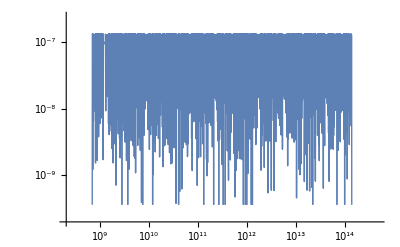

```mathematica
LogLogPlot[{
Abs[1/f[h] approximation[xP,yP,tgPout,tgPin][h]-1]},
{h,xP//First,xP//Last},PlotStyle->Thick,
ImageSize->Full,Ticks->{10.^Range[-18,30],Flatten@Outer[Times,10.^Range[-18,30],Range[1,9,1]]},
GridLines->{Flatten@Outer[Times,10.^Range[-18,30],Range[1,9,1]],Flatten@Outer[Times,10.^Range[-18,30],Range[1,9,1]]},
GridLinesStyle->Lighter@Gray,ClippingStyle->Red
]
```

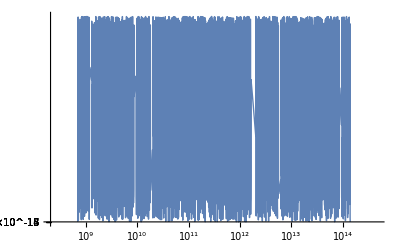

```mathematica
LogLinearPlot[{
Abs[1/f[h] approximation[xP,yP,tgPout,tgPin][h]-1]},
{h,xP//First,xP//Last},PlotStyle->Thick,
ImageSize->Full,Ticks->{10.^Range[-18,30],Flatten@Outer[Times,10.^Range[-18,30],Range[1,9,1]]},
GridLines->{Flatten@Outer[Times,10.^Range[-18,30],Range[1,9,1]],Flatten@Outer[Times,10.^Range[-18,30],Range[1,9,1]]},
GridLinesStyle->Lighter@Gray,ClippingStyle->Red
]
```

## Output.

```mathematica
keyFrames[xP,yP,tgPin,tgPout]
```

key =   6.96342e8               46153.606505845986        -0.0001325601687269933     -0.0001325590196060018
key =   7.179279380019401e8     43419.92968612424         -0.00012096012282829791    -0.00012095797100986462
key =   7.401830194986337e8     40848.16846781357         -0.0001103741643431477     -0.00011037220071778014
key =   7.631279873003552e8     38428.73259438066         -0.00010071464763056876    -0.00010071285564523206
key =   7.867842272247182e8     36152.59983991784         -0.00009190049440465655    -0.00009189885875091389
key =   8.1117378802929e8       34011.28236470514         -0.00008385772084158044    -0.00008385622934344798
key =   8.363194019620976e8     31996.795063531205        -0.0000765188202985727     -0.0000765174586493428
key =   8.622445059491808e8     30101.62578874261         -0.00006982219117989438    -0.0000698209490453472
key =   8.88973263438938e8      28318.70733698086         -0.00006371162538386756    -0.0000637104915890644
key =   9.16530586923627e8      26641.391095144318        -0.00005813583198969281    -0.00005813479793222246
key =   9.449421611590102e8     25063.42224729897         -0.00005304801069177682    -0.000053047066811886666
key =   9.742344671037868e8     23578.916450083296        -0.000048405455538363604   -0.00004840459420566356
key =   1.0044348066011251e9    22182.337889628143        -0.00004416919849799342    -0.00004416841279461395
key =   1.0355713278252975e9    20868.478638164645        -0.00004030368225075063    -0.00004030296573318294
key =   1.0676730515171381e9    19632.439233339726        -0.00003677646139964991    -0.000036775807016582723
key =   1.1007698980327744e9    18469.610407818178        -0.000033557928636858793   -0.00003355733171174835
key =   1.134892715230843e9     17375.65590103984         -0.000030621069503747095   -0.00003062052477508949
key =   1.1700733072241833e9    16346.496289036006        -0.00002794123290435777    -0.000027940735778646296
key =   1.2063444640228057e9    15378.293772005294        -0.00002549592502510084    -0.000025495471507923524
key =   1.2437399920957642e9    14467.437862920977        -0.000023264621027476026   -0.00002326420724761577
key =   1.2822947458804169e9    13610.53192380174         -0.000021228592144201356   -0.000021228214452544136
key =   1.322044660268445e9     12804.380499438686        -0.000019370748448983643   -0.000019370403867068802
key =   1.3630267840989058e9    12045.977401345384        -0.000017675496041253574   -0.00001767518160060617
key =   1.4052793146895392e9    11332.4944974952          -0.000016128605520987252   -0.000016128318634754234
key =   1.448841633438512e9     10661.271166042156        -0.000014717092837879421   -0.000014716831035961074
key =   1.4937543425297825e9    10029.804373697643        -0.000013429110253437073   -0.000013428871318116366
key =   1.5400593027762947e9    9435.739341764589         -0.000012253846854908118   -0.000012253628854711718
key =   1.5877996726362777e9    8876.860765022137         -0.000011181437949218123   -0.000011181238954143175
key =   1.6370199484390118e9    8351.084550715575         -0.000010202882031181893   -0.000010202700522393262
key =   1.6877660058575559e9    7856.450046845637         -9.309965543368507e-6      -9.30979999066646e-6
key =   1.740085142667088e9     7391.112730776018         -8.495193677288772e-6      -8.495042553308193e-6
key =   1.7940261228287168e9    6953.337330894462         -7.75172744023053e-6       -7.751589524507242e-6
key =   1.8496392219398456e9    6541.491355677674         -7.0733264741866655e-6     -7.073200605791735e-6
key =   1.9069762740934572e9    6154.039006029524         -6.454296489698369e-6      -6.454181659437658e-6
key =   1.9660907201899905e9    5789.535448191298         -5.889441619225818e-6      -5.889336836172653e-6
key =   2.027037657746839e9     5446.621425867319         -5.374020619419834e-6      -5.3739250529013084e-6
key =   2.089873892251897e9     5124.018191474198         -4.903707307172762e-6      -4.903620063967745e-6
key =   2.1546579901090174e9    4820.522737612075         -4.474553942022235e-6      -4.474474339538701e-6
key =   2.2214503332247252e9    4535.003310975662         -4.082958422197203e-6      -4.0828857910061056e-6
key =   2.290313175287071e9     4266.395191976224         -3.7256338198000018e-6     -3.725567535764226e-6
key =   2.3613106997890735e9    4013.6967243364224        -3.3995808683095635e-6     -3.3995203852537744e-6
key =   2.4345090798508315e9    3775.9655798521494        -3.1020627990818646e-6     -3.1020075988308613e-6
key =   2.5099765398960686e9    3552.3152443924164        -2.8305823375914495e-6     -2.830531998615203e-6
key =   2.587783419240587e9     3341.911712033364         -2.582860810502628e-6      -2.5828148758338903e-6
key =   2.668002237651908e9     3143.970374998628         -2.3568189139728905e-6     -2.3567769727095586e-6
key =   2.7507077629411936e9    2957.7530978084474        -2.150559298562206e-6      -2.1505210353895413e-6
key =   2.8359770806504574e9    2782.565464726838         -1.9623507292154127e-6     -1.9623158197191358e-6
key =   2.92388966590001e9      2617.7541902423936        -1.7906134397841276e-6     -1.7905815869465282e-6
key =   3.0145274574631085e9    2462.7046829262385        -1.6339059308963886e-6     -1.6338768639378181e-6
key =   3.1079749341368475e9    2316.838753582604         -1.4909128534276317e-6     -1.4908863259791267e-6
key =   3.2043191934804773e9    2179.6124591455805        -1.3604339665186132e-6     -1.3604097654892592e-6
key =   3.3036500329945326e9    2050.5140742818044        -1.241374090693849e-6      -1.241352005105741e-6
key =   3.406060033816438e9     1929.0621831350672        -1.1327338696562042e-6     -1.132713715415241e-6
key =   3.511644647010598e9     1814.8038840968288        -1.03360141534324e-6       -1.033583026969141e-6
key =   3.6205022825333953e9    1707.3131009081283        -9.431446473391725e-7      -9.431278690001589e-7
key =   3.732734400956022e9     1606.188993794882         -8.606043035878518e-7      -8.605889943853394e-7
key =   3.8484456080306287e9    1511.054464711589         -7.852875695938193e-7      -7.8527359822119e-7
key =   3.9677437521879363e9    1421.5547511194147        -7.165622640060101e-7      -7.165495118817109e-7
key =   4.090740025057179e9     1337.3561030547564        -6.538515253034259e-7      -6.53839892140435e-7
key =   4.21754906510207e9      1258.144538555            -5.966289887953394e-7      -5.966183722861558e-7
key =   4.348289064469383e9     1183.624672800378         -5.444143424582046e-7      -5.444046597255145e-7
key =   4.483081879149742e9     1113.518616605716         -4.967693236935983e-7      -4.967604822576696e-7
key =   4.622053142553282e9     1047.5649401544927        -4.5329400500912776e-7     -4.532859435414022e-7
key =   4.765332382606054e9     985.5176981108873         -4.136234835063723e-7      -4.13616123075692e-7
key =   4.913053142476308e9     927.1455124744297         -3.7742476630367257e-7     -3.7741805308372553e-7
key =   5.065353105043165e9     872.2307097571305         -3.4439402328523926e-7     -3.443878955321301e-7
key =   5.222374221223716e9     820.5685092655937         -3.1425400057691467e-7     -3.1424840853971917e-7
key =   5.384262842278119e9     771.9662594611533         -2.867517143871035e-7      -2.86746613557574e-7
key =   5.551169856216048e9     726.2427195503783         -2.616563224625051e-7      -2.6165166696223385e-7
key =   5.723250828431595e9     683.2273836269532         -2.3875718048383204e-7     -2.3875293231471264e-7
key =   5.90066614669773e9      642.7598448446142         -2.1786208208885985e-7     -2.1785820740761658e-7
key =   6.083581170655446e9     604.6891972501058         -1.9879564307296011e-7     -1.9879210526785613e-7
key =   6.27216638593693e9      568.8734730455548         -1.8139782187574112e-7     -1.813945953420091e-7
key =   6.466597563066397e9     535.1791131817755         -1.655225919182005e-7      -1.6551964707346238e-7
key =   6.667055921286709e9     503.4804693083232         -1.5103669983755968e-7     -1.510340122984682e-7
key =   6.873728297464453e9     473.65933522302805        -1.378185562933408e-7      -1.378161045783677e-7
key =   7.086807320230923e9     445.6045060737612         -1.257572135045312e-7      -1.257549762926093e-7
key =   7.3064915895213e9       419.21136366866864        -1.1475143256284455e-7     -1.14749390658295e-7
key =   7.532985861679383e9     394.38148634846783        -1.0470883411598316e-7     -1.0470697148789205e-7
key =   7.766501240300381e9     371.02228196599657        -9.55451250966981e-8       -9.554342553457981e-8
key =   8.0072553729896555e9    349.0466426043739         -8.718338844922972e-8      -8.718183682636149e-8
key =   8.2554726542207985e9    328.37261974619463        -7.955343753419247e-8      -7.955202268418093e-8
key =   8.51138443448211e9      308.9231186824419         -7.259123120447233e-8      -7.2589939323832e-8
key =   8.775229235906424e9     290.62561102155365        -6.623832925348738e-8      -6.623715102851386e-8
key =   9.047252974585245e9     273.41186422656693        -6.044140878919595e-8      -6.044033389381804e-8
key =   9.327709189774427e9     257.2176871717705         -5.5151812315799263e-8     -5.51508311699784e-8
key =   9.616859280204988e9     241.98269077003002        -5.0325140692841347e-8     -5.03242453311824e-8
key =   9.914972747719353e9     227.6500627781495         -4.5920880615292084e-8     -4.5920063504470424e-8
key =   1.0222327448460075e10   214.16635594050504        -4.1902064115759964e-8     -4.1901318524843175e-8
key =   1.0539209851845179e10   201.48128868092533        -3.823495870434271e-8      -3.823427846815569e-8
key =   1.0865915307571484e10   189.54755759958618        -3.488878414314875e-8      -3.488816338248474e-8
key =   1.120274832089478e10    178.32066107570935        -3.183545379407467e-8      -3.183488718459731e-8
key =   1.1550022836443422e10   167.75873331826793        -2.9049338828830996e-8     -2.904882195184361e-8
key =   1.1908062530829887e10   157.8223882458641         -2.6507053891113515e-8     -2.6506582285701996e-8
key =   1.2277201114332994e10   148.47457261359713        -2.4187259875881635e-8     -2.4186829467081302e-8
key =   1.2657782641931993e10   139.68042783922354        -2.2070485078815566e-8     -2.2070092558030574e-8
key =   1.305016183398242e10    131.40716001334872        -2.01389623541375e-8       -2.013860402965134e-8
key =   1.3454704406832584e10   123.62391760891265        -1.8376478890886297e-8     -1.8376151862590875e-8
key =   1.387178741368887e10    116.30167643393818        -1.676824101195576e-8      -1.676794273550708e-8
key =   1.4301799596047512e10   109.41313139852551        -1.530074992482906e-8      -1.5300477694343395e-8
key =   1.4745141746020447e10   102.93259469248432        -1.3961687872473932e-8     -1.3961439588698042e-8
key =   1.5202227079892906e10   96.8358999939017          -1.2739815444545824e-8     -1.2739588719631682e-8
key =   1.567348162326094e10    91.10031235143458         -1.1624876354848585e-8     -1.162466963443283e-8
key =   1.6159344608107838e10   85.70444340427042         -1.060751255973851e-8      -1.0607323773739157e-8
key =   1.666026888218954e10    80.62817162360835         -9.679184336635612e-9      -9.679012185038563e-9
key =   1.7176721331110611e10   75.85256727823423         -8.832099895239152e-9      -8.831942729712132e-9
key =   1.770918331348415e10    71.3598218443833          -8.059148935740743e-9      -8.059005536869941e-9
key =   1.8258151109581272e10   67.13318159665413         -7.353843611446536e-9      -7.353712778453826e-9
key =   1.882413638388826e10    63.15688513233128         -6.71026387107474e-9       -6.7101444989981055e-9
key =   1.9407666662002575e10   59.416104596140364        -6.123007733276323e-9      -6.1228988308428805e-9
key =   2.0009285822312176e10   55.89689038625931         -5.58714597391062e-9       -5.587046553091356e-9
key =   2.0629554602916435e10   52.58611913539098         -5.0981807086249e-9        -5.098090016466965e-9
key =   2.126905112426111e10    49.47144477291541         -4.652007801731124e-9      -4.6519250585097076e-9
key =   2.1928371427974506e10   46.54125248562941         -4.244882212697743e-9      -4.244806709544737e-9
key =   2.260813003240706e10    43.784615405390255        -3.873386681382176e-9      -3.873317761597445e-9
key =   2.3308960505392086e10   41.19125386214907         -3.5344029709349576e-9     -3.5343400860169564e-9
key =   2.4031516054761597e10   38.751497050425854        -3.2250858064897464e-9     -3.225028407419436e-9
key =   2.477647013716753e10    36.45624696627813         -2.942838847568401e-9      -2.942786510164622e-9
key =   2.5544517085775856e10   34.29694448028189         -2.6852930706010048e-9     -2.6852453030895007e-9
key =   2.633637275741861e10    32.26553742000904         -2.4502866889287128e-9     -2.4502430934886048e-9
key =   2.715277519980701e10    30.35445054297873         -2.235847138860775e-9      -2.2358073719413296e-9
key =   2.799448533942756e10    28.556557288109886        -2.0401745186243336e-9     -2.040138216207057e-9
key =   2.8862287690762257e10   26.86515320033456         -1.8616263855774844e-9     -1.8615932815457029e-9
key =   2.975699108749397e10    25.27393092927052         -1.6987041119575269e-9     -1.6986738835477245e-9
key =   3.0679429436378468e10   23.77695670872193         -1.550040141122348e-9      -1.5500125668000272e-9
key =   3.163046249448578e10    22.36864822929839         -1.4143866695151216e-9     -1.4143615075055008e-9
key =   3.2610976670535282e10   21.04375382163823         -1.2906050605453505e-9     -1.290582100020613e-9
key =   3.362188585107141e10    19.797332872608898        -1.1776563311109232e-9     -1.1776353931565183e-9
key =   3.4664132252250046e10   18.624737401455167        -1.0745924494206812e-9     -1.0745733211666876e-9
key =   3.573868729802945e10    17.521594727191708        -9.805482977463908e-10     -9.805308551157216e-10
key =   3.684655252558428e10    16.48379116260536         -8.947345351402062e-10     -8.947186184845464e-10
key =   3.7988760518786606e10   15.507456674061313        -8.164308569292553e-10     -8.164163308000916e-10
key =   3.916637587062389e10    14.588950449908472        -7.449800075787252e-10     -7.449667573861343e-10
key =   4.038049617545108e10    13.724847323667783        -6.797822641537255e-10     -6.797701675137533e-10
key =   4.1632253052001495e10   12.911925001374762        -6.202903665587412e-10     -6.202793315174454e-10
key =   4.292281319811014e10    12.14715204544611         -5.66004971886576e-10      -5.659949032176585e-10
key =   4.42533794781324e10     11.427676570261616        -5.164704248382735e-10     -5.164612333512313e-10
key =   4.5625192044071686e10   10.750815607306441        -4.712709431315848e-10     -4.712625625146532e-10
key =   4.703952949146096e10    10.114045100215648        -4.3002714876501514e-10    -4.30019497005686e-10
key =   4.84977100510755e10     9.514990492412082         -3.923928475211823e-10     -3.9238586754769665e-10
key =   5.000109281758762e10    8.951417872238075         -3.5805215559668364e-10    -3.580457847807179e-10
key =   5.155107901630851e10    8.421225642560842         -3.2671682615021957e-10    -3.2671101278625197e-10
key =   5.314911330919785e10    7.922436683786863         -2.9812384233575616e-10    -2.98118538837368e-10
key =   5.4796685141358536e10   7.453190981060728         -2.7203320576963784e-10    -2.720283669183224e-10
key =   5.649533012927137e10    7.011738688154773         -2.482259196831579e-10     -2.4822150409543704e-10
key =   5.824663149206378e10    6.596433602184363         -2.2650215467587277e-10    -2.2649812525239846e-10
key =   6.005222152714646e10    6.205727024815571         -2.066795694868491e-10     -2.0667589164899535e-10
key =   6.191378313159335e10    5.8381619870733905        -1.8859177854015499e-10    -1.885884234185965e-10
key =   6.383305137068297e10    5.492367816214356         -1.7208696127279467e-10    -1.720838995360744e-10
key =   6.581181509506297e10    5.167055024403187         -1.570265806573564e-10     -1.570237876325864e-10
key =   6.785191860804535e10    4.861010500132942         -1.43284226765378e-10      -1.4328167772223843e-10
key =   6.995526338458612e10    4.573092984457232         -1.3074454993231482e-10    -1.3074222301962104e-10
key =   7.212380984355179e10    4.30222881516508          -1.1930229564127712e-10    -1.1930017355068304e-10
key =   7.435957917492435e10    4.047407923028166         -1.088614242054797e-10     -1.0885948717467598e-10
key =   7.666465522364792e10    3.807680065190259         -9.933429635924387e-11     -9.933252936777852e-11
key =   7.904118643187286e10    3.5821512816528616        -9.064094587371922e-11     -9.063933338045961e-11
key =   8.149138784140755e10    3.3699805616431346        -8.270840358293833e-11     -8.270693240026213e-11
key =   8.401754315824422e10    3.1703767074327422        -7.547008655845999e-11     -7.546874389824158e-11
key =   8.662200688108327e10    2.9825953839126216        -6.886523862767364e-11     -6.886401358924306e-11
key =   8.930720649583966e10    2.8059363429213553        -6.283842122058984e-11     -6.283730361200272e-11
key =   9.207564473817699e10    2.6397408119765022        -5.7339047705149247e-11    -5.7338027660270723e-11
key =   9.492990192617793e10    2.4833890376712895        -5.232095758559805e-11     -5.232002691395887e-11
key =   9.787263836532527e10    2.3362979745758583        -4.7742031380483667e-11    -4.774118202044843e-11
key =   1.00906596828035e11     2.197919111024818         -4.356383474744757e-11     -4.356306010162274e-11
key =   1.0403460511005264e11   2.0677364236833435        -3.9751298007800214e-11    -3.975059060240776e-11
key =   1.072595786660954e11    1.945264453264271         -3.627241909162499e-11     -3.6271773830307514e-11
key =   1.1058452332719662e11   1.830046494220406         -3.309799842569748e-11     -3.309740948827349e-11
key =   1.1401253810228554e11   1.721652891661315         -3.0201390540211984e-11    -3.020085320362261e-11
key =   1.1754681806661308e11   1.6196794391436817        -2.755828240952922e-11     -2.755779236069854e-11
key =   1.2119065733971631e11   1.5237458713604968        -2.514648913181606e-11     -2.5146041725550922e-11
key =   1.249474521556968e11    1.4334944461082297        -2.294576643085652e-11     -2.294535809157156e-11
key =   1.288207040286748e11    1.3485886102440368        -2.093764220917997e-11     -2.09372698429969e-11
key =   1.3281402301636943e11   1.2687117446582905        -1.910526143764306e-11     -1.9104921566402536e-11
key =   1.369311310848467e11    1.1935659835823542        -1.7433243394788972e-11    -1.743293335790994e-11
key =   1.411758655775716e11    1.1228711038287167        -1.5907553947502346e-11    -1.5907270891045716e-11
key =   1.455521827919974e11    1.0563634798214114        -1.4515386735075684e-11    -1.4515128548538617e-11
key =   1.5006416166702594e11   0.993795100519945         -1.3245056690631183e-11    -1.3244821064500735e-11
key =   1.5471600758477545e11   0.9349326445708028        -1.2085900955503007e-11    -1.2085685948924645e-11
key =   1.595120562901999e11    0.8795566102376976        -1.102819002056821e-11     -1.1027993820892383e-11
key =   1.6445677793221234e11   0.8274604968660314        -1.0063045820785274e-11    -1.006286675768298e-11
key =   1.695547812300797e11    0.7784500348291897        -9.182367246619535e-12     -9.182203902107756e-12
key =   1.7481081776897156e11   0.7323424610850967        -8.378762271238207e-12     -8.378613195637044e-12
key =   1.8022978642866675e11   0.6889658376415373        -7.645485645598505e-12     -7.64534963414235e-12
key =   1.8581673794954602e11   0.6481584103887551        -6.976382535616963e-12     -6.976258434142839e-12
key =   1.9157687964012573e11   0.6097680059083814        -6.365836729694618e-12     -6.365723484781644e-12
key =   1.975155802305208e11    0.5736514640093522        -5.808723522964208e-12     -5.808620149673733e-12
key =   2.0363837487636044e11   0.5396741038747076        -5.300366659105592e-12     -5.30027236501004e-12
key =   2.099509703178202e11    0.5077092218285012        -4.836499227296742e-12     -4.836413179164248e-12
key =   2.164592501985794e11    0.4776376188499618        -4.413227646535491e-12     -4.413149167200605e-12
key =   2.2316928054966116e11   0.44934715607297715       -4.026999194199691e-12     -4.026927533914148e-12
key =   2.30087315443266e11     0.42273233661333226       -3.674571899237693e-12     -3.6745065459161195e-12
key =   2.3721980282186902e11   0.39769391216430666       -3.3529877025511794e-12    -3.3529280424221584e-12
key =   2.4457339050801364e11   0.3741385128936058        -3.059547288782375e-12     -3.059492835151659e-12
key =   2.521549324004031e11    0.3519782992614846        -2.7917876108419068e-12    -2.791737962227514e-12
key =   2.599714948620649e11    0.3311306344616747        -2.5474612503132753e-12    -2.547415937957796e-12
key =   2.6803036330654224e11   0.3115177762636272        -2.3245173845667145e-12    -2.3244760088460685e-12
key =   2.763390489882511e11    0.29306658710693          -2.1210846606961133e-12    -2.121046945154686e-12
key =   2.8490529600333203e11   0.2757082613668234        -1.9354556041582505e-12    -1.9354211869813858e-12
key =   2.9373708850752155e11   0.2593780687737742        -1.7660720836520935e-12    -1.7660406489080743e-12
key =   3.028426581577706e11    0.24401511303029952       -1.6115123281079837e-12    -1.6114836599555387e-12
key =   3.122304917845465e11    0.22956210472490918       -1.4704790524927745e-12    -1.4704528874480323e-12
key =   3.2190933930196826e11   0.21596514769634997       -1.341788454719531e-12     -1.3417645828204664e-12
key =   3.318882218631491e11    0.2031735380514891        -1.2243603562965538e-12    -1.2243385782147894e-12
key =   3.421764402683467e11    0.1911395750873628        -1.1172091103532217e-12    -1.1171892356292801e-12
key =   3.527835836337578e11    0.1798183834123069        -1.0194353236801013e-12    -1.019417191730613e-12
key =   3.6371953832903766e11   0.16916774560284778       -9.302183210327492e-13     -9.302017664680064e-13
key =   3.749944971918736e11    0.15914794477232086       -8.488092363558883e-13     -8.487941370393238e-13
key =   3.8661896902820184e11   0.14972161646414536       -7.74524761128731e-13      -7.745109803920873e-13
key =   3.9860378840692206e11   0.1408536093174566        -7.067413707516426e-13     -7.067288000351377e-13
key =   4.1096012575823834e11   0.1325108539855087        -6.44890118989289e-13      -6.448786513586131e-13
key =   4.236994977850396e11    0.1246622398180365        -5.884518518657005e-13     -5.884413810359121e-13
key =   4.368337781970226e11    0.11727849884771832       -5.36952836623973e-13      -5.369432868913274e-13
key =   4.503752087775623e11    0.1103320966481164        -4.899608178890935e-13     -4.899521041243483e-13
key =   4.643364107936454e11    0.10379712965609914       -4.470813583336893e-13     -4.470734036676029e-13
key =   4.787303967594999e11    0.09764922857585331       -4.0795453986696065e-13    -4.079472803314619e-13
key =   4.9357058256488684e11   0.09186546750427362       -3.7225194708546917e-13    -3.7224532511126577e-13
key =   5.088707999793572e11    0.08642427843885304       -3.3967390726832793e-13    -3.3966786652264504e-13
key =   5.246453095441286e11    0.08130537084926857       -3.0994697209543664e-13    -3.0994145792235707e-13
key =   5.409088138635984e11    0.07648965601273953       -2.828216213889753e-13     -2.8281658906840457e-13
key =   5.576764713088805e11    0.0719591758310005        -2.58070175214303e-13      -2.58065582323139e-13
key =   5.749639101461389e11    0.06769703586344306       -2.3548487866952174e-13    -2.3548068950303816e-13
key =   5.927872431028866e11    0.06368734232670233       -2.1487616033141334e-13    -2.1487233684775517e-13
key =   6.111630823858251e11    0.059915142825756766      -1.9607103598780215e-13    -1.9606754741819098e-13
key =   6.301085551642228e11    0.05636637059552289       -1.7891166310666008e-13    -1.7890848028188872e-13
key =   6.496413195332642e11    0.05302779204501873       -1.6325401161091072e-13    -1.6325110703816102e-13
key =   6.697795809722462e11    0.04988695740848536       -1.4896665663454388e-13    -1.4896400640543795e-13
key =   6.905421093129644e11    0.046932154319440776      -1.3592967512071901e-13    -1.359272573730297e-13
key =   7.119482562341017e11    0.0441523641345414        -1.2403363979634588e-13    -1.2403143386511358e-13
key =   7.340179732979276e11    0.04153722084438006       -1.1317869944203869e-13    -1.1317668560217589e-13
key =   7.567718305461172e11    0.039076972417996264      -1.0327374058811803e-13    -1.0327190310879961e-13
key =   7.802310356720226e11    0.03676244443694994       -9.423562536642951e-14     -9.423394871900344e-14
key =   8.044174537872675e11    0.034585005883348084      -8.598849064288582e-14     -8.59869609540802e-14
key =   8.29353627801086e11     0.032536536954245576      -7.846311313709127e-14     -7.846171715912174e-14
key =   8.550627994314033e11    0.030609398782398156      -7.159632732319442e-14     -7.159505321702166e-14
key =   8.815689308672374e11    0.02879640495045435       -6.53304955601403e-14      -6.532933334690644e-14
key =   9.088967271026172e11    0.027090794692360944      -5.96130253824835e-14      -5.961196469784833e-14
key =   9.370716589628286e11    0.025486207682048605      -5.439592553796156e-14     -5.439495805674837e-14
key =   9.66119986844454e11     0.02397666031538278       -4.9635406239800296e-14    -4.963452315845937e-14
key =   9.96068785191329e11     0.02255652339693412       -4.529150889437607e-14     -4.529070311194798e-14
key =   1.0269459677292311e12   0.021220501148360774      -4.1327772425334674e-14    -4.132703746861484e-14
key =   1.05878031348282e12     0.019963611460123633      -3.7710926974383163e-14    -3.7710256161393926e-14
key =   1.0916014935990773e12   0.018781167312891957      -3.441061374782341e-14     -3.4410001577898946e-14
key =   1.1254400990022483e12   0.0176687592993586        -3.1399130959770274e-14    -3.139857216766692e-14
key =   1.1603276689060598e12   0.016622239181287617      -2.8651201238378e-14       -2.865069156810778e-14
key =   1.1962967202097898e12   0.01563770442047752       -2.614375978673897e-14     -2.614329476987016e-14
key =   1.2333807778055874e12   0.0147114836259551        -2.385575988758239e-14     -2.3855335401106967e-14
key =   1.2716144058252905e12   0.013840122863131608      -2.1767996636617566e-14    -2.1767609492426376e-14
key =   1.3110332398558655e12   0.01302037277386715       -1.9862946521978876e-14    -1.9862593053308415e-14
key =   1.3516740201534941e12   0.01224917645941341       -1.812461877736463e-14     -1.8124296400055623e-14
key =   1.3935746258872664e12   0.011523658081049236      -1.6538422822739116e-14    -1.653812856949576e-14
key =   1.436774110444394e12    0.010841112135900331      -1.5091044452575146e-14    -1.509077606460271e-14
key =   1.481312737829853e12    0.010198993367951808      -1.3770335113749284e-14    -1.3770090162176067e-14
key =   1.52723202019438e12     0.009594907276631206      -1.2565209047756934e-14    -1.2564985507166367e-14
key =   1.5745747565257998e12   0.009026601187567856      -1.1465550893023027e-14    -1.14653469454147e-14
key =   1.6233850725397498e12   0.008491955852230917      -1.0462130596387208e-14    -1.0461944430212013e-14
key =   1.6737084618069749e12   0.007988977545120646      -9.546525690744464e-15     -9.546355844751064e-15
key =   1.7255918281555334e12   0.007515790629042754      -8.711050950692857e-15     -8.710896026284736e-15
key =   1.779083529387428e12    0.007070630560741402      -7.948693759091215e-15     -7.948552325834013e-15
key =   1.8342334223504114e12   0.00665183731080834       -7.25305506527942e-15      -7.252925994253846e-15
key =   1.891092909406976e12    0.006257849173330643      -6.61829591570325e-15      -6.618178206329007e-15
key =   1.949714986343837e12    0.005887196942192822      -6.039088456882386e-15     -6.038981032117928e-15
key =   2.0101542917665625e12   0.005538498432316443      -5.510570966158452e-15     -5.510472951650258e-15
key =   2.0724671580253936e12   0.0052104533254065215     -5.0283072711730255e-15    -5.028217834222175e-15
key =   2.1367116637197122e12   0.00490183832098424       -4.5882494200299125e-15    -4.588167791320985e-15
key =   2.2029476878301006e12   0.004611502574623855      -4.186703697819039e-15     -4.186629253451685e-15
key =   2.2712369655284414e12   0.004338363406382698      -3.820299731571756e-15     -3.820231769387826e-15
key =   2.3416431457180776e12   0.004081402263420764      -3.4859619970221455e-15    -3.4858999581673555e-15
key =   2.4142318503576636e12   0.0038396609217542154     -3.1808841725585652e-15    -3.1808275870226335e-15
key =   2.489070735623998e12    0.003612237912978911      -2.9025055919922374e-15    -2.9024539507135568e-15
key =   2.5662295549708467e12   0.0033982851626390273     -2.6484896080328387e-15    -2.648442498988579e-15
key =   2.6457802241425283e12   0.0031970048277049847     -2.4167041340282733e-15    -2.4166611255141463e-15
key =   2.7277968882028604e12   0.0030076463213674883     -2.2052035920571108e-15    -2.2051643728983055e-15
key =   2.812355990641938e12    0.0028295035140529115     -2.0122127791583958e-15    -2.0121769744464082e-15
key =   2.899536344625156e12    0.0026619121002224902     -1.8361117574475075e-15    -1.836079085315776e-15
key =   2.9894192064508833e12   0.002504247121135897      -1.6754224140762126e-15    -1.6753925981213168e-15
key =   3.0820883512852573e12   0.0023559206343414804     -1.5287959692013934e-15    -1.5287687729930408e-15
key =   3.1776301512446816e12   0.0022163795212025174     -1.3950017032906478e-15    -1.3949768907846336e-15
key =   3.2761336558988076e12   0.002085103424283637      -1.2729165954055581e-15    -1.272893945333869e-15
key =   3.377690675269032e12    0.001961602806905781      -1.1615158896805775e-15    -1.1614952276928285e-15
key =   3.482395865399871e12    0.0018454171276336701     -1.059864549440165e-15     -1.0598456919782415e-15
key =   3.5903468165829595e12   0.0017361131228883285     -9.671093329831219e-16     -9.670921305187637e-16
key =   3.7016441443159165e12   0.0016332831912804183     -8.824716939380812e-16     -8.824559972532649e-16
key =   3.816391583080845e12    0.0015365438736394687     -8.052412127421446e-16     -8.052268855264862e-16
key =   3.934696083029878e12    0.0014455344230709277     -7.347696396410383e-16     -7.347565643896819e-16
key =   4.05666790966788e12     0.0013599154597086975     -6.704654629476782e-16     -6.7045353576291195e-16
key =   4.182420746625224e12    0.0012793677051466347     -6.117889382774834e-16     -6.117780554454427e-16
key =   4.3120718016164214e12   0.0012035907918296449     -5.582475527878419e-16     -5.582376263961187e-16
key =   4.445741915683369e12    0.0011323021429645013     -5.093919066159952e-16     -5.09382840999702e-16
key =   4.583555675825035e12    0.0010652359187735218     -4.648119094748725e-16     -4.648036417124542e-16
key =   4.725641531118555e12    0.0010021420251616043     -4.24133383121922e-16      -4.24125840094162e-16
key =   4.872131912439973e12    0.0009427851810998883     -3.8701488363201487e-16    -3.8700799792011726e-16
key =   5.02316335589621e12     0.000886944041248261      -3.531448482792289e-16     -3.5313856728258433e-16
key =   5.17887663008331e12     0.0008344103705448979     -3.222389886006701e-16     -3.2223325491917717e-16
key =   5.339416867289561e12    0.0007849882676848515     -2.9403788801260017e-16    -2.940326558220951e-16
key =   5.504933698765798e12    0.0007384934345919752     -2.6830483729045523e-16    -2.683000644438667e-16
key =   5.675581394188951e12    0.0006947524891600061     -2.4482384419907406e-16    -2.4481948795132507e-16
key =   5.851519005448831e12    0.0006536023186999767     -2.2339781538896783e-16    -2.233938401342499e-16
key =   6.032910514892169e12    0.0006148894716829145     -2.0384690858084368e-16    -2.0384328261955914e-16
key =   6.219924988162078e12    0.0005784695855096069     -1.860070221953918e-16     -1.8600371249604267e-16
key =   6.4127367317753955e12   0.0005442068481735473     -1.697284120715939e-16     -1.6972539278811798e-16
key =   6.6115254555847705e12   0.000511973491809567      -1.5487444285636129e-16    -1.5487168820293313e-16
key =   6.816476440276922e12    0.0004816493162395703     -1.4132043593664257e-16    -1.4131792149606818e-16
key =   7.027780710063181e12    0.00045312124073864133    -1.2895262218549938e-16    -1.2895032731950606e-16
key =   7.245635210723279e12    0.00042628288235003136    -1.1766719076467326e-16    -1.1766509792760333e-16
key =   7.470242993168323e12    0.00040103415917653787    -1.0736941755176497e-16    -1.0736750628489256e-16
key =   7.701813402694043e12    0.000377280917168925      -9.797286410228829e-17     -9.797112099262544e-17
key =   7.940562274100716e12    0.0003549345790196535     -8.939866076681705e-17     -8.939707032920849e-17
key =   8.186712132861616e12    0.00033391181385262754    -8.157483855525882e-17     -8.15733869372458e-17
key =   8.440492402527501e12    0.00031413422647720655    -7.443572665273298e-17     -7.443440194559615e-17
key =   8.702139618560435e12    0.0002955280650476943     -6.792140164508493e-17     -6.79201933271912e-17
key =   8.971897648796256e12    0.000278023946038148      -6.197718535892287e-17     -6.197608286471252e-17
key =   9.250017920741174e12    0.0002615565955069217     -5.65531838309403e-17      -5.655217749430196e-17
key =   9.536759655914342e12    0.0002460646056861036     -5.1603869385928025e-17    -5.160295128405754e-17
key =   9.832390111454824e12    0.0002314902059881544     -4.7087699828133894e-17    -4.708686230241836e-17
key =   1.0137184829218154e13   0.00021777904757581504    -4.29667680426536e-17      -4.2966003442344805e-17
key =   1.0451427892594643e13   0.0002048800006919345     -3.9206483724825764e-17    -3.920578637311246e-17
key =   1.0775412191288812e13   0.00019274496399344427    -3.577528522836406e-17     -3.57746485792667e-17
key =   1.110943969430674e13    0.00018132868517847805    -3.264437151930989e-17     -3.264379091606158e-17
key =   1.1453821731405748e13   0.00017058859223774024    -2.978746343608959e-17     -2.9786933483712825e-17
key =   1.1808879283268768e13   0.00016048463470085293    -2.7180580710894034e-17    -2.7180097163084668e-17
key =   1.2174943280673828e13   0.00015097913428567598    -2.480184225214781e-17     -2.4801401114877073e-17
key =   1.255235491293752e13    0.00014203664439366436    -2.26312817437315e-17      -2.2630879074105672e-17
key =   1.2941465945919902e13   0.00013362381792731136    -2.0650680140813374e-17    -2.0650312650064067e-17
key =   1.3342639049887271e13   0.00012570928293676107    -1.8843413049080942e-17    -1.8843077811919228e-17
key =   1.3756248137538357e13   0.00011826352563186795    -1.7194310997668716e-17    -1.7194005137044043e-17
key =   1.4182678712509e13      0.00011125878032344973    -1.5689531918045218e-17    -1.568925281122069e-17
key =   1.4622328228680156e13   0.00010466892588331612    -1.431644522536175e-17     -1.4316190518044944e-17
key =   1.50756064606241e13     0.00009846938833696746    -1.3063525717694191e-17    -1.3063293374998176e-17
key =   1.55429358855341e13     0.00009263704922572486    -1.1920256905800934e-17    -1.192004480303898e-17
key =   1.6024752076993568e13   0.00008715015939656907    -1.0877042418008626e-17    -1.0876848970444583e-17
key =   1.6521504110951658e13   0.00008198825789820448    -9.925126096102036e-18     -9.924949518304693e-18
key =   1.703365498428373e13    0.00007713209568090731    -9.056517738759419e-18     -9.056356622266964e-18
key =   1.756168204632679e13    0.00007256356381562937    -8.26392660641302e-18      -8.263779573313051e-18
key =   1.810607744379211e13    0.00006826562596468246    -7.540699946084856e-18     -7.540565804577188e-18
key =   1.8667348579469727e13   0.00006422225485218206    -6.880767298916142e-18     -6.880644870001887e-18
key =   1.9246018585152336e13   0.000060418372497345174   -6.27858935749532e-18      -6.2784776383741934e-18
key =   1.9842626809219367e13   0.000056839793987767924   -5.7291116629602e-18       -5.729009750111436e-18
key =   2.0457729319335723e13   0.00005347317458301049    -5.227722142183957e-18     -5.22762916136842e-18
key =   2.1091899420733676e13   0.000050305959951235297   -4.770212296265449e-18     -4.7701274036023316e-18
key =   2.1745728190561023e13   0.00004732633935332767    -4.352741888283547e-18     -4.352664461063637e-18
key =   2.241982502879352e13    0.0000445232015999196     -3.971806892988467e-18     -3.971736221807453e-18
key =   2.3114818226225074e13   0.00004188609361707796    -3.624209828075578e-18     -3.6241453547852096e-18
key =   2.3831355550065098e13   0.00003940518146614568    -3.307033110758971e-18     -3.306974277070688e-18
key =   2.457010484768882e13    0.000037071213672376685   -3.017614462808587e-18     -3.017560778137179e-18
key =   2.533175466910327e13    0.00003487548672561485    -2.753524612285726e-18     -2.7534756123876685e-18
key =   2.6117014908709125e13   0.000032809812624366646   -2.5125468646993782e-18    -2.5125021553313022e-18
key =   2.6926617466956566e13   0.0000308664883422375     -2.292658544096369e-18     -2.29261776312765e-18
key =   2.776131693251183e13    0.00002903826710287026    -2.092014000962614e-18     -2.091976798248694e-18
key =   2.8621891285570254e13   0.0000273183313562683     -1.908929104522784e-18     -1.908895130338551e-18
key =   2.9509142622971402e13   0.000025700267355730248   -1.7418670583206646e-18    -1.7418360747254243e-18
key =   3.042389790579201e13    0.000024178041240592048   -1.5894256470867112e-18    -1.589397367688732e-18
key =   3.1367009730113656e13   0.000022745976535587664   -1.4503253083563625e-18    -1.450299507009097e-18
key =   3.2339357121683438e13   0.000021398732982921965   -1.3233984913092043e-18    -1.3233749408123565e-18
key =   3.334184635520843e13    0.000020131286628119355   -1.2075798054072988e-18    -1.2075583303980476e-18
key =   3.4375411799047438e13   0.000018938911085386992   -1.1018971283704078e-18    -1.1018775350667952e-18
key =   3.544101678608742e13    0.000017817159912630076   -1.005463396380533e-18     -1.0054454973634753e-18
key =   3.653965451161626e13    0.000016761850030394493   -9.17469150188837e-19      -9.17452834125899e-19
key =   3.767234895902868e13    0.000015769046122904884   -8.371758285433516e-19     -8.371609362825524e-19
key =   3.8840155854228234e13   0.000014835045963029011   -7.639094641407023e-19     -7.638958715287283e-19
key =   4.004416364961479e13    0.000013956366606443904   -6.970550830263272e-19     -6.970426832177573e-19
key =   4.128549453857471e13    0.000013129731403521206   -6.360515385101e-19        -6.360402217211318e-19
key =   4.256530550141928e13    0.000012352057780498218   -5.803867846042768e-19     -5.803764627637815e-19
key =   4.388478938374618e13    0.000011620445744369806   -5.295935971029476e-19     -5.295841764167941e-19
key =   4.524517600822919e13    0.000010932167068635235   -4.832456304309843e-19     -4.832370317762578e-19
key =   4.6647733320872266e13   0.000010284655119572963   -4.409538558474581e-19     -4.409460109795382e-19
key =   4.8093768572796445e13   9.675495285104814e-6      -4.0236329342871154e-19    -4.023561338543804e-19
key =   4.958462953866098e13    9.102415970558339e-6      -3.6715002559358713e-19    -3.6714349339860173e-19
key =   5.112170577285438e13    8.563280127749858e-6      -3.3501848617660737e-19    -3.350125267610048e-19
key =   5.270642990462621e13    8.056077285799717e-6      -3.0569897389304465e-19    -3.0569353589728164e-19
key =   5.4340278973366664e13   7.578916053962113e-6      -2.789453910469474e-19     -2.7894042838172793e-19
key =   5.60247758052786e13     7.1300170685121026e-6     -2.545331775221529e-19     -2.545286496268282e-19
key =   5.7761490432725086e13   6.7077063573883005e-6     -2.3225742667081003e-19    -2.3225329312253077e-19
key =   5.955204155757532e13    6.310409097847598e-6      -2.119311610380491e-19     -2.1192739025421654e-19
key =   6.139809805991294e13    5.9366437438538185e-6     -1.9338377222400253e-19    -1.933803312391475e-19
key =   6.3301380553512805e13   5.5850165013009825e-6     -1.7645957782571887e-19    -1.7645643873209536e-19
key =   6.526366298953612e13    5.254216130468942e-6      -1.6101652389465458e-19    -1.6101365861206205e-19
key =   6.728677430993851e13    4.943009056329422e-6      -1.4692498500211743e-19    -1.4692237015942836e-19
key =   6.937260015213224e13    4.6502347684685006e-6     -1.3406668211348047e-19    -1.340642981025446e-19
key =   7.152308460649131e13    4.374801493471533e-6      -1.2233368963821484e-19    -1.2233151257194822e-19
key =   7.374023202833753e13    4.115682123632637e-6      -1.1162752168041738e-19    -1.1162553506306343e-19
key =   7.60261089060964e13     3.871910386806555e-6      -1.0185831558279316e-19    -1.0185650380736461e-19
key =   7.838284578736416e13    3.642577243120108e-6      -9.294407289626129e-20     -9.294241942964586e-20
key =   8.081263926468088e13    3.426827495106329e-6      -8.480996978936326e-20     -8.480846122717144e-20
key =   8.331775402286084e13    3.2238565986202493e-6     -7.738773190665024e-20     -7.738635509548362e-20
key =   8.59005249497881e13     3.0329076626440566e-6     -7.061505922020495e-20     -7.061380300369188e-20
key =   8.856335931264461e13    2.8532686267937094e-6     -6.443510452634945e-20     -6.44339581789642e-20
key =   9.13087390015996e13     2.6842696060017524e-6     -5.879599539441414e-20     -5.879494898639332e-20
key =   9.413922284305086e13    2.5252803924745043e-6     -5.3650398694481344e-20    -5.364944450464037e-20
key =   9.70574489845746e13     2.3757081056082332e-6     -4.895512502310229e-20     -4.895425418625129e-20
key =   1.0006613735380622e14   2.2349949811007547e-6     -4.467076332833782e-20     -4.466996852385766e-20
key =   1.0316809219354428e14   2.102616291013867e-6      -4.076135217180416e-20     -4.0760627037172205e-20
key =   1.063662046754401e14    1.97807838703044e-6       -3.719407753948827e-20     -3.719341590282699e-20
key =   1.0966345559470925e14   1.8609168596093323e-6     -3.393899685091854e-20     -3.3938392973372885e-20
key =   1.1306291814837672e14   1.7506948061735065e-6     -3.096878816911698e-20     -3.096823703114154e-20
key =   1.1656776079964477e14   1.6470012018733192e-6     -2.825852036039901e-20     -2.8258017762794815e-20
key =   1.2018125023105364e14   1.549449366849448e-6      -2.5785444907031158e-20    -2.5784986064078528e-20
key =   1.2390675438918739e14   1.457675524279803e-6      -2.3528803226751634e-20    -2.3528384603756725e-20
key =   1.2774774562376267e14   1.3713374438332685e-6     -2.1469654068343223e-20    -2.1469272104028025e-20
key =   1.3170780392402628e14   1.2901131654716495e-6     -1.959071356372118e-20     -1.9590365112257013e-20
key =   1.3579062025547795e14   1.2136997988407884e-6     -1.787621073243022e-20     -1.7875892648503323e-20
key =   1.4000000000002839e14   1.1418123937737163e-6     -1.6311754387255274e-20    -1.6311605625335498e-20